## Convergencia numérica

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Paquetes a importar

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["MieTheory`"]
Needs["GoldenSectionSearchMaxMin`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

```mathematica
<< "MieTheory.wl"
```

```mathematica
cp=ResourceFunction["CombinePlots"];
```

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

omega10=Range[0,10,0.01]; 
omegaVis=Range[2,3.1,0.01];
energyTicksMajorVisible={2.07,2.26,2.48,2.76,3.1};

epsPlasma=1.823;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
bluelight30=RGBColor[0/255,170/255,212/255];
bluedark30=RGBColor[0/255,51/255,128/255];
greenlight30=RGBColor[137/255,160/255,44/255];
greendark30=RGBColor[68/255,80/255,22/255];
bluemedium30=RGBColor[55/255,171/255,200/255];
redlight34=RGBColor[255/255,42/255,42/255];
reddark34=RGBColor[128/255,0/255,0/255];
colorsCHCM={bluelight30,bluedark30,bluemedium30,redlight34,reddark34,greenlight30,greendark30}
colors2={blueUNAM, redUNAM};
colors={Blue,Red};
color5={Orange};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
rojos=Table[RGBColor[1,g,0],{g,0,0.9,0.16}]
sunsetColors=Table[ColorData["SunsetColors"][i],{i,0,0.8,1/7}]
solarColors=Table[ColorData["SolarColors"][i],{i,0,0.8,1/7}]
alpineColors=Table[ColorData["AlpineColors"][i],{i,0,0.8,1/7}]
lakeColors=Table[ColorData["LakeColors"][i],{i,0,0.8,1/7}]
candyColors=Table[ColorData["CandyColors"][i],{i,0,0.8,1/7}]
verde=RGBColor[150/255,200/255,60/255];


lajolla = ColorMapSuite["lajolla"];
```

{RGBColor[0, Rational[2, 3], Rational[212, 255]],RGBColor[0, Rational[1, 5], Rational[128, 255]],RGBColor[Rational[11, 51], Rational[57, 85], Rational[40, 51]],RGBColor[1, Rational[14, 85], Rational[14, 85]],RGBColor[Rational[128, 255], 0, 0],RGBColor[Rational[137, 255], Rational[32, 51], Rational[44, 255]],RGBColor[Rational[4, 15], Rational[16, 51], Rational[22, 255]]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[1, 0., 0],RGBColor[1, 0.16, 0],RGBColor[1, 0.32, 0],RGBColor[1, 0.48, 0],RGBColor[1, 0.64, 0],RGBColor[1, 0.8, 0]}

{RGBColor[0., 0., 0.],RGBColor[0.3195368571428571, 0.1164, 0.4341454285714286],RGBColor[0.6695744285714286, 0.22438285714285713, 0.338128],RGBColor[0.8974812857142858, 0.3693308571428571, 0.1452665142857143],RGBColor[0.9882154285714286, 0.5505617142857143, 0.08483494285714285],RGBColor[1., 0.7397017142857143, 0.23300614285714283]}

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.6706774285714285, 0.06984285714285714, 0.009042057142857144],RGBColor[0.8432481428571429, 0.15849014285714286, 0.008003357142857142],RGBColor[0.9277247142857143, 0.30355071428571423, 0.024193185714285713],RGBColor[0.978545, 0.4534661428571428, 0.0459689],RGBColor[0.995709, 0.6082364285714286, 0.07333049999999999]}

{RGBColor[0.277546, 0.355398, 0.484215],RGBColor[0.3092687142857143, 0.43180485714285716, 0.45451742857142857],RGBColor[0.35382528571428573, 0.4807017142857143, 0.3698534285714286],RGBColor[0.43932542857142853, 0.5335538571428571, 0.38461414285714285],RGBColor[0.5610134285714286, 0.5994675714285714, 0.49026099999999995],RGBColor[0.6995328571428572, 0.6994642857142856, 0.6226554285714285]}

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.40930385714285716, 0.25890179999999996, 0.6923064285714285],RGBColor[0.5251917142857143, 0.46039919999999995, 0.8552008571428571],RGBColor[0.6206238571428572, 0.6188315714285714, 0.9107938571428571],RGBColor[0.7058281428571428, 0.7557314285714285, 0.9127361428571429],RGBColor[0.7881374285714285, 0.8555037142857143, 0.9026041428571429]}

{RGBColor[0.405188, 0.204349, 0.343389],RGBColor[0.6033010000000001, 0.22473442857142858, 0.36270257142857143],RGBColor[0.7647998571428571, 0.3022755714285714, 0.4413708571428571],RGBColor[0.8306595714285715, 0.45290014285714286, 0.5840857142857143],RGBColor[0.7940618571428572, 0.5946167142857143, 0.7287942857142857],RGBColor[0.7161124285714285, 0.7039788571428571, 0.8368194285714285]}

## Funciones

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]

errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]


errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> (Directive[#, Thickness[0.003]] & /@ colorsCHCM),  
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
   LabelStyle->{FontFamily->"Latin Modern Roman 10"},
   ImagePadding->{{90,10},{60,60}}};
  
plotPolarStyling = {PlotMarkers->{"●",4.5},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colorsCHCM),
    PlotRange -> 270, 
    Joined->True,
    PolarAxes -> True,
    PolarTicks -> {Drop[Table[i, {i, 0, 2 Pi, Pi/6}], -1], Automatic},
    PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 50, 100,150}},
    GridLinesStyle -> Directive[Gray, Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
 ImagePadding->{{50,20},{5,5}}};
  
  
  
  SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Figuras\\4-Resultados"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Figuras\4-Resultados

## Eritrocito sano

### Convergencia numérica

```mathematica
dataEriSanoCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Cabs_12_11_10.csv"];
dataEriSanoCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Csca_12_11_10.csv"];

dataQabsEriSano=Transpose[{dataEriSanoCabs[[All,1]],dataEriSanoCabs[[All,#]]/(Pi*3750^2)}]&/@Range[2,4];
dataQscaEriSano=Transpose[{dataEriSanoCsca[[All,1]],dataEriSanoCsca[[All,#]]/(Pi*3750^2)}]&/@Range[2,4];
```

```mathematica
hola=Interpolation[Transpose[{dataEriSanoCabs[[All,1]],dataQext[dataQabsEriSano[[3]],dataQscaEriSano[[3]]][[All,2]]}]]
```

InterpolatingFunction[…]

```mathematica
MinimalBy[Table[{x,hola[x]},{x,430,450}],Last]
```

{{440,0.749463}}

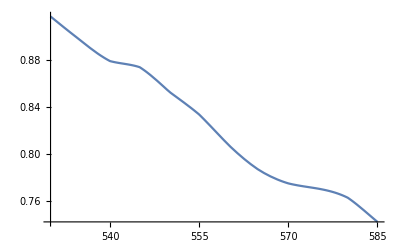

```mathematica
Plot[hola[x],{x,530,585}]
```

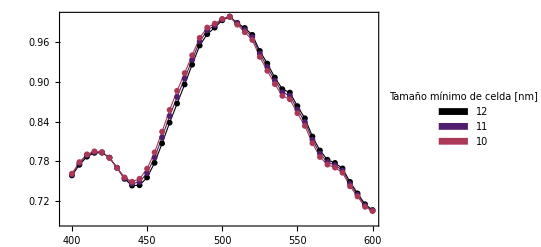

```mathematica
plotEriSano=ListPlot[dataQext[dataQabsEriSano[[#]],dataQscaEriSano[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.2}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

### Propiedades ópticas

#### Importación y preparación de datos

```mathematica
dataEriSano=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_Cabs_Csca.csv"];
dataQabsEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,2]]/(Pi*3750^2)}];
dataQscaEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,3]]/(Pi*3750^2)}];

dataCabsEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,2]]}];
dataCscaEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,3]]}];
```

```mathematica
Plot[{dataQabsEriSanoFinal}]
```

#### Qext

```mathematica
ymin = Min[dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal][[All, 2]]];
ymax = Max[dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal][[All, 2]]];
```

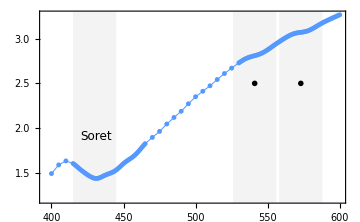

```mathematica
qExt30=ListPlot[{dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal]},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.2,Automatic}},
                      PlotStyle -> Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                       Prolog -> {
                      {
                      FaceForm[Directive[LightGray, Opacity[0.3]]],  EdgeForm[Transparent], Rectangle[{415, 0}, {445, 3.5}],Rectangle[{526, 0}, {556, 3.5}],Rectangle[{558, 0}, {588, 3.5}] },
                      Text[Style["Soret", 12, FontFamily->"Latin Modern Roman 10"],  {431, 1.9}],Text[Style[MaTeX["\\beta"], Magnification->1.05, FontFamily->"Latin Modern Roman 10"],  {541, 2.5}],
                      Text[Style[Style[MaTeX["\\alpha"], Magnification->1.05, FontFamily->"Latin Modern Roman 10"]],  {573, 2.5}] },
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["Qext_EriSano.svg",qExt30]
```

Qext_EriSano.svg

```mathematica
MinimalBy[dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal],Last]
```

{{431,1.43507}}

#### lambda = 431 nm

```mathematica
dataEriSanoFF431=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_431.csv"];

dataThetaEriSano431=Drop[dataEriSanoFF431,1][[All,1]];
dataPhiEriSano431=Drop[dataEriSanoFF431,1][[All,2]];
dataRCSEriSano431=Drop[dataEriSanoFF431,1][[All,3]];

data431 = Transpose[{dataThetaEriSano431 *Pi/180, dataPhiEriSano431*Pi/180, dataRCSEriSano431}];
data431Linear = Transpose[{dataThetaEriSano431 *Pi/180, dataPhiEriSano431*Pi/180, 10^(dataRCSEriSano431/10)}];
fInterp431 = Interpolation[data431,InterpolationOrder->1];
fInterp431Linear = Interpolation[data431Linear,InterpolationOrder->1];
min431 = Min[dataRCSEriSano431];
max431 = Max[dataRCSEriSano431];
```

```mathematica
dataFF4310=Table[{th,fInterp431[Abs[If[th > Pi, th - 2 Pi, th]], 0]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF431Pi=Table[{th,fInterp431[Abs[If[th > Pi, th - 2 Pi, th]], Pi]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF431Pi2=Table[{th,fInterp431[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]/(4 Pi)}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF431PiDegree=Table[{th*180/Pi,fInterp431[th, Pi]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF431Pi2DegreeLinear=Table[{th*180/Pi,fInterp431Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF4310DegreeLinear=Table[{th*180/Pi,fInterp431Linear[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

```mathematica
dataFF4310Theta=Table[{ph,fInterp431[0,Abs[If[ph > Pi, ph - 2 Pi, ph]]]/(4 Pi)}, {ph, 0, 2 Pi,Pi/100}];
dataFF431PiTheta=Table[{ph,fInterp431[Pi,Abs[If[ph > Pi, ph - 2 Pi, ph]]]/(4 Pi)}, {ph, 0,  2 Pi,Pi/100}];
dataFF431Pi2Theta=Table[{ph,fInterp431[Pi/2,Abs[If[ph > Pi, ph - 2 Pi, ph]]]/(4 Pi)}, {ph, 0,  2 Pi,Pi/100}];
```

```mathematica
fInterp431Linear[0, Pi/2]/(4 Pi)
fInterp431Linear[0, Pi/3]/(4 Pi)
```

1.26122×10^10

1.26122×10^10

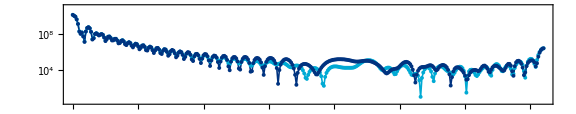

```mathematica
linearplot431FF=ListPlot[{dataFF4310DegreeLinear,dataFF431Pi2DegreeLinear},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(0.5),10^(11)}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.3]&/@{MaTeX["\\varphi=0^{\\circ}"],MaTeX["\\varphi=90^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.8,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[1]], Thickness[0.002]],Directive[colorsCHCM[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["linearplot431FF_EriSano.svg",linearplot431FF]
```

linearplot431FF_EriSano.svg

```mathematica
polarplot431FF = ListPolarPlot[
 {dataFF4310Theta, dataFF431PiTheta,dataFF431Pi2Theta},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 20, 40, 60, 80, 100}
 },

 PlotLegends -> Placed[
   {
    Style[MaTeX["\\varphi=0^{\\circ}"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=90^{\\circ}"], Magnification -> 1.7]
   },
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-180,0},{-180,120}}],

 (* ticks *)
   Table[   Line[{     {-183,r},     { -180,r}   }],
   {r,0,120,20}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-181.5,r},{ -180,r}}], {r,0,120,5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-205,r} ], {r,0,120,20}]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colorsCHCM),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 150
]
```

-Graphics-

```mathematica
polarplot431FF = ListPolarPlot[
 {dataFF4310, dataFF431Pi2},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 2, 4, 6, 8, 10}
 },

  
 PlotLegends -> Placed[SwatchLegend[
   {
    Style[MaTeX["\\varphi=0^{\\circ}"], Magnification -> 1.9, Black],
    Style[MaTeX["\\varphi=90^{\\circ}"], Magnification -> 1.9]
   }],
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-15.0,0},{-15.0,10}}],

 (* ticks *)
   Table[   Line[{     {-15.3,r},     { -15.0,r}   }],
   {r,0,10,2}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-15.15,r},{ -15,r}}], {r,0,10,0.5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-16.5,r} ], {r,0,10,2}],
     Text[Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{dB}] "], Magnification->2],  {-16,12.0} ]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {bluelight30,bluedark30}),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->2],
   PlotRange -> 12
]
```

-Graphics-

```mathematica
Export["polarplot431FF_EriSano.svg",polarplot431FF]
```

polarplot431FF_EriSano.svg

```mathematica
Export["linearplot431FF_EriSano.svg",linearplot431FF]
```

polarplot431FF_EriSano.svg

linearplot431FF_EriSano.svg

```mathematica
data = Flatten[Table[{fInterp440[th, ph], th, ph}, {th, 0, Pi, Pi/100}, {ph, 0, 2 Pi, 2 Pi/100}], 1];
mapping =  CoordinateTransformData["Spherical" -> "Cartesian", "Mapping"];
ListPointPlot3D[mapping /@ data, BoxRatios -> Automatic]
```

InterpolatingFunction::dmval: Input value {0,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {π/100,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {π/50,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
cf431 = ColorMapSuite["lapaz"];
```

```mathematica
plotEriSano431axes=SphericalPlot3D[
 fInterp431[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
 PlotPoints -> 100,

 ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp431[th, ph],
       {min431, max431}
     ]
   ]
 ],
 ColorFunctionScaling -> False,

 PlotStyle -> Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 Mesh -> False,
 Exclusions -> None,

PlotLegends -> BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,\\,\\, "],Magnification->1.4]
],
 LabelStyle -> {
   Black,
   FontFamily -> "Latin Modern Roman 10",
   FontSize -> 18
 },
  ViewPoint -> {1, 1, 0}, 
  ViewVertical -> {0, -1, 0}
]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotEriSano431noaxes0=SphericalPlot3D[fInterp431[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
  ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp431[th, ph],
       {min431, max431}
     ]
   ]
 ],
 
 ColorFunctionScaling -> False,
 
 PlotPoints -> 100,
 Boxed -> False,
 Axes -> False,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
PlotLegends -> Placed[BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,\\,\\, "],Magnification->1.6]
],Top],
   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->20},
   ViewPoint -> {1, 1, 0}, 
  ViewVertical -> {0, -1, 0}
 ];

planeX=ParametricPlot3D[{0,y,z},{y,-100,100},{z,-100,120},PlotStyle->Directive[colorsCHCM[[2]],Opacity[0.35]],Mesh->None];

planeY=ParametricPlot3D[{x,0,z},{x,-100,100},{z,-100,120},PlotStyle->Directive[RGBColor[44/255,160/255,90/255],Specularity[100],Opacity[0.2]],Mesh->None];

plotEriSano431noaxes=Show[plotEriSano431noaxes0,planeX,planeY,PlotRange->All,Lighting->"Neutral"]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
colorsCHCM[[1]]
```

RGBColor[0, Rational[2, 3], Rational[212, 255]]

```mathematica
Export["FFdistribution431axes_EriSano.svg",plotEriSano431axes]
```

FFdistribution431axes_EriSano.svg

```mathematica
Export["FFdistribution431_EriSano.svg",plotEriSano431noaxes]
```

FFdistribution431_EriSano.svg

```mathematica
Export["grafica_editable.svg", graficaFinal, ]
```

#### lambda = 541 nm

```mathematica
dataEriSanoFF541=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_541.csv"];

dataThetaEriSano541=Drop[dataEriSanoFF541,1][[All,1]];
dataPhiEriSano541=Drop[dataEriSanoFF541,1][[All,2]];
dataRCSEriSano541=Drop[dataEriSanoFF541,1][[All,3]];

data541 = Transpose[{dataThetaEriSano541 *Pi/180, dataPhiEriSano541*Pi/180, dataRCSEriSano541}];
data541Linear = Transpose[{dataThetaEriSano541 *Pi/180, dataPhiEriSano541*Pi/180, 10^(dataRCSEriSano541/10)}];
fInterp541 = Interpolation[data541,InterpolationOrder->1];
fInterp541Linear = Interpolation[data541Linear,InterpolationOrder->1];
min541 = Min[dataRCSEriSano541];
max541 = Max[dataRCSEriSano541];
```

```mathematica
dataFF5410=Table[{th,fInterp541[Abs[If[th > Pi, th - 2 Pi, th]], 0]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF541Pi=Table[{th,fInterp541[Abs[If[th > Pi, th - 2 Pi, th]], Pi]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF541Pi2=Table[{th,fInterp541[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]/(4 Pi)}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF541PiDegree=Table[{th*180/Pi,fInterp541[th, Pi]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF541Pi2DegreeLinear=Table[{th*180/Pi,fInterp541Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF5410DegreeLinear=Table[{th*180/Pi,fInterp541Linear[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

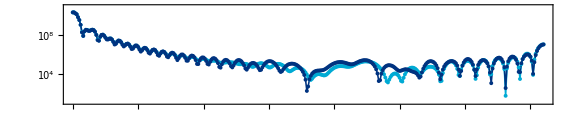

```mathematica
linearplot541FF=ListPlot[{dataFF5410DegreeLinear,dataFF541Pi2DegreeLinear},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(1),10^(11
                      )}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1]&/@{MaTeX["\\varphi=0^{\\circ}"],MaTeX["\\varphi=90^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.8,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[1]], Thickness[0.002]],Directive[colorsCHCM[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.05],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.05],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.25],
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["linearplot541FF_EriSano.svg",linearplot541FF]
```

linearplot541FF_EriSano.svg

```mathematica
polarplot541FF = ListPolarPlot[
 {dataFF5410, dataFF541Pi2},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 2, 4, 6, 8, 10}
 },

  
 PlotLegends -> Placed[SwatchLegend[
   {
    Style[MaTeX["\\varphi=0^{\\circ}"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=90^{\\circ}"], Magnification -> 1.7]
   }],
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-15.0,0},{-15.0,10}}],

 (* ticks *)
   Table[   Line[{     {-15.3,r},     { -15.0,r}   }],
   {r,0,10,2}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-15.15,r},{ -15,r}}], {r,0,10,0.5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-16.5,r} ], {r,0,10,2}],
     Text[Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{dB}] "], Magnification->1.8],  {-16,12.0} ]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {bluelight30,bluedark30}),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 12
]
```

-Graphics-

```mathematica
Export["polarplot541FF_EriSano.svg",polarplot541FF]
```

polarplot541FF_EriSano.svg

```mathematica
N[331 Pi/360]*180/Pi
N[389 Pi/360]*180/Pi
```

165.5

194.5

```mathematica
MinimalBy[dataFF5410,Last]
```

{{(331 π)/360,2.21225},{(389 π)/360,2.21225}}

```mathematica
cf541 = ColorMapSuite["oslo"];
```

```mathematica
plotEriSano541axes=SphericalPlot3D[
 fInterp541[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
 PlotPoints -> 100,

 ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp541[th, ph],
       {min541, max541}
     ]
   ]
 ],
 ColorFunctionScaling -> False,

 PlotStyle -> Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 Mesh -> False,
 Exclusions -> None,

PlotLegends -> BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,\\,\\, "],Magnification->1.4]
],
 LabelStyle -> {
   Black,
   FontFamily -> "Latin Modern Roman 10",
   FontSize -> 18
 },
  ViewPoint -> {1, 12, 0}, 
  ViewVertical -> {0, -1, 0}
]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotEriSano541noaxes0=SphericalPlot3D[fInterp541[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
  ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp541[th, ph],
       {min541, max541}
     ]
   ]
 ],
 
 ColorFunctionScaling -> False,
 
 PlotPoints -> 100,
 Boxed -> False,
 Axes -> False,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
PlotLegends -> Placed[BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)/(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)_{\\text{max}}\\,\\,\\, "],
 Magnification->1.6]
],Top],
   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->20},
   ViewPoint -> {1, 1, 0}, 
  ViewVertical -> {0, -1, 0}
 ];

planeX=ParametricPlot3D[{0,y,z},{y,-100,100},{z,-100,120},PlotStyle->Directive[colorsCHCM[[2]],Opacity[0.35]],Mesh->None];

planeY=ParametricPlot3D[{x,0,z},{x,-100,100},{z,-100,120},PlotStyle->Directive[RGBColor[44/255,160/255,90/255],Specularity[100],Opacity[0.2]],Mesh->None];

plotEriSano541noaxes=Show[plotEriSano541noaxes0,planeX,planeY,PlotRange->All]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["FFdistribution541axes_EriSano.svg",plotEriSano541axes]
```

FFdistribution541axes_EriSano.svg

```mathematica
Export["FFdistribution541_EriSano.svg",plotEriSano541noaxes]
```

FFdistribution541_EriSano.svg

```mathematica
Export["grafica_editable.svg", graficaFinal, ]
```

#### lambda = 573 nm

```mathematica
dataEriSanoFF573=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_573.csv"];

dataThetaEriSano573=Drop[dataEriSanoFF573,1][[All,1]];
dataPhiEriSano573=Drop[dataEriSanoFF573,1][[All,2]];
dataRCSEriSano573=Drop[dataEriSanoFF573,1][[All,3]];

data573 = Transpose[{dataThetaEriSano573 *Pi/180, dataPhiEriSano573*Pi/180, dataRCSEriSano573}];
data573Linear = Transpose[{dataThetaEriSano541 *Pi/180, dataPhiEriSano573*Pi/180, 10^(dataRCSEriSano573/10)}];
fInterp573 = Interpolation[data573,InterpolationOrder->1];
fInterp573Linear = Interpolation[data573Linear,InterpolationOrder->1];
min573 = Min[dataRCSEriSano573];
max573 = Max[dataRCSEriSano573];
```

```mathematica
dataFF5730=Table[{th,fInterp573[Abs[If[th > Pi, th - 2 Pi, th]], 0]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF573Pi=Table[{th,fInterp573[Abs[If[th > Pi, th - 2 Pi, th]], Pi]/(4 Pi)}, {th, 0,  2 Pi,Pi/360}];
dataFF573Pi2=Table[{th,fInterp573[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]/(4 Pi)}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF573PiDegree=Table[{th*180/Pi,fInterp573[th, Pi]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF573Pi2DegreeLinear=Table[{th*180/Pi,fInterp573Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF5730DegreeLinear=Table[{th*180/Pi,fInterp573Linear[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

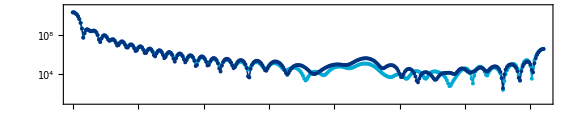

```mathematica
linearplot573FF=ListPlot[{dataFF5730DegreeLinear,dataFF573Pi2DegreeLinear},PlotMarkers->{"●",4},
                      Joined->True,
                      ScalingFunctions->"Log",
                      PlotRange->{{Automatic,Automatic},{10^(1),10^(11)}},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1]&/@{MaTeX["\\varphi=0^{\\circ}"],MaTeX["\\varphi=90^{\\circ}"]},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    
                                    Spacings->0.05],{0.8,0.8}],
                      PlotStyle -> {Directive[colorsCHCM[[1]], Thickness[0.002]],Directive[colorsCHCM[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{nm}^2] "],Magnification->1.05],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.05],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Large,
                      AspectRatio->2/10,
                      FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.25],
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["linearplot573FF_EriSano.svg",linearplot573FF]
```

linearplot573FF_EriSano.svg

```mathematica
polarplot573FF = ListPolarPlot[
 {dataFF5730, dataFF573Pi2},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 2, 4, 6, 8, 10}
 },

  
 PlotLegends -> Placed[SwatchLegend[
   {
    Style[MaTeX["\\varphi=0^{\\circ}"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=90^{\\circ}"], Magnification -> 1.7]
   }],
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-15.0,0},{-15.0,10}}],

 (* ticks *)
   Table[   Line[{     {-15.3,r},     { -15.0,r}   }],
   {r,0,10,2}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-15.15,r},{ -15,r}}], {r,0,10,0.5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-16.5,r} ], {r,0,10,2}],
     Text[Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,[\\text{dB}] "], Magnification->1.8],  {-16,12.0} ]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {bluelight30,bluedark30}),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 12
]
```

-Graphics-

```mathematica
Export["polarplot573FF_EriSano.svg",polarplot573FF]
```

polarplot573FF_EriSano.svg

```mathematica
cf541 = ColorMapSuite["oslo"];
```

```mathematica
plotEriSano573axes=SphericalPlot3D[
 fInterp573[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
 PlotPoints -> 100,

 ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp573[th, ph],
       {min541, max541}
     ]
   ]
 ],
 ColorFunctionScaling -> False,

 PlotStyle -> Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 Mesh -> False,
 Exclusions -> None,

PlotLegends -> BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\,\\,\\, "],Magnification->1.4]
],
 LabelStyle -> {
   Black,
   FontFamily -> "Latin Modern Roman 10",
   FontSize -> 18
 },
  ViewPoint -> {1, 12, 0}, 
  ViewVertical -> {0, -1, 0}
]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotEriSano573noaxes0=SphericalPlot3D[fInterp573[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},
  ColorFunction -> Function[{x, y, z, th, ph},
   cf431[
     Rescale[
       fInterp573[th, ph],
       {min541, max541}
     ]
   ]
 ],
 
 ColorFunctionScaling -> False,
 
 PlotPoints -> 100,
 Boxed -> False,
 Axes -> False,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
PlotLegends -> Placed[BarLegend[
 {cf431, {0, 1}},
 Ticks -> ({#, NumberForm[#, {2, 2}]} & /@ Range[0, 1, 0.25]), LegendLabel->Style[MaTeX["(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)/(\\text{d}C_{\\text{sca}}/\\text{d}\\Omega)_{\\text{max}}\\,\\,\\, "],
 Magnification->1.6]
],Top],
   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->20},
   ViewPoint -> {1, 1, 0}, 
  ViewVertical -> {0, -1, 0}
 ];

planeX=ParametricPlot3D[{0,y,z},{y,-100,100},{z,-100,120},PlotStyle->Directive[colorsCHCM[[2]],Opacity[0.35]],Mesh->None];

planeY=ParametricPlot3D[{x,0,z},{x,-100,100},{z,-100,120},PlotStyle->Directive[RGBColor[44/255,160/255,90/255],Specularity[100],Opacity[0.2]],Mesh->None];

plotEriSano573noaxes=Show[plotEriSano573noaxes0,planeX,planeY,PlotRange->All]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["FFdistribution573axes_EriSano.svg",plotEriSano573axes]
```

FFdistribution573axes_EriSano.svg

```mathematica
Export["FFdistribution573_EriSano.svg",plotEriSano573noaxes]
```

FFdistribution573_EriSano.svg

```mathematica
Export["grafica_editable.svg", graficaFinal, ]
```

#### lambda=632.8

```mathematica
dataEriSanoFF632circ=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_632_circ.csv"];

dataThetaEriSano632circ=Drop[dataEriSanoFF632circ,1][[All,1]];
dataPhiEriSano632circ=Drop[dataEriSanoFF632circ,1][[All,2]];
dataRCSEriSano632circ=Drop[dataEriSanoFF632circ,1][[All,3]];

data632circ = Transpose[{dataThetaEriSano632circ *Pi/180, dataPhiEriSano632circ*Pi/180, dataRCSEriSano632circ}];
data632circLinear = Transpose[{dataThetaEriSano632circ *Pi/180, dataPhiEriSano632circ*Pi/180, 10^(dataRCSEriSano632circ/10)}];
fInterp632circ = Interpolation[data632circ,InterpolationOrder->1];
fInterp632circLinear = Interpolation[data632circLinear,InterpolationOrder->1];
```

```mathematica
dataEriSanoFF632lat=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_632_lat.csv"];

dataThetaEriSano632lat=Drop[dataEriSanoFF632lat,1][[All,1]];
dataPhiEriSano632lat=Drop[dataEriSanoFF632lat,1][[All,2]];
dataRCSEriSano632lat=Drop[dataEriSanoFF632lat,1][[All,3]];

data632lat = Transpose[{dataThetaEriSano632lat *Pi/180, dataPhiEriSano632lat*Pi/180, dataRCSEriSano632lat}];
data632latLinear = Transpose[{dataThetaEriSano632lat *Pi/180, dataPhiEriSano632lat*Pi/180, 10^(dataRCSEriSano632lat/10)}];
fInterp632lat = Interpolation[data632lat,InterpolationOrder->1];
fInterp632latLinear = Interpolation[data632latLinear,InterpolationOrder->1];
```

```mathematica
res1=NIntegrate[
 (fInterp632circLinear[th, phi]/(4 Pi))*
  Sin[th]*
  Boole[
    Abs[Sin[phi]] >= (2.2 Degree)/th
  ],
 {th, 2.2 Degree, 8.2 Degree},
 {phi, 0, 2 Pi},
 Method -> "LocalAdaptive"
]

res2=NIntegrate[
 (fInterp632latLinear[th, phi]/(4 Pi))*
  Sin[th]*
  Boole[
    Abs[Sin[phi]] >= (2.2 Degree)/th
  ],
 {th, 2.2 Degree, 8.2 Degree},
 {phi, 0, 2 Pi},
 Method -> "LocalAdaptive"
]
```

2.60768×10^7

7.04948×10^6

```mathematica
res1/(10^(6))
res2/(10^(6))
```

26.0768

7.04948

```mathematica
dataEriSanoFF632circ344=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_632_circ_344.csv"];

dataThetaEriSano632circ344=Drop[dataEriSanoFF632circ344,1][[All,1]];
dataPhiEriSano632circ344=Drop[dataEriSanoFF632circ344,1][[All,2]];
dataRCSEriSano632circ344=Drop[dataEriSanoFF632circ344,1][[All,3]];

data632circ344 = Transpose[{dataThetaEriSano632circ344 *Pi/180, dataPhiEriSano632circ344*Pi/180, dataRCSEriSano632circ344}];
data632circLinear344 = Transpose[{dataThetaEriSano632circ344 *Pi/180, dataPhiEriSano632circ344*Pi/180, 10^(dataRCSEriSano632circ344/10)}];
fInterp632circ344 = Interpolation[data632circ344,InterpolationOrder->1];
fInterp632circLinear344 = Interpolation[data632circLinear344,InterpolationOrder->1];
```

```mathematica
dataEriSanoFF632lat344=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_632_lat_344.csv"];

dataThetaEriSano632lat344=Drop[dataEriSanoFF632lat344,1][[All,1]];
dataPhiEriSano632lat344=Drop[dataEriSanoFF632lat344,1][[All,2]];
dataRCSEriSano632lat344=Drop[dataEriSanoFF632lat344,1][[All,3]];

data632lat344 = Transpose[{dataThetaEriSano632lat344 *Pi/180, dataPhiEriSano632lat344*Pi/180, dataRCSEriSano632lat344}];
data632latLinear344 = Transpose[{dataThetaEriSano632lat344 *Pi/180, dataPhiEriSano632lat344*Pi/180, 10^(dataRCSEriSano632lat344/10)}];
fInterp632lat344 = Interpolation[data632lat344,InterpolationOrder->1];
fInterp632latLinear344 = Interpolation[data632latLinear344,InterpolationOrder->1];
```

```mathematica
res1=NIntegrate[
 (fInterp632circLinear344[th, phi]/(4 Pi))*
  Sin[th]*
  Boole[
    Abs[Sin[phi]] >= (2.2 Degree)/th
  ],
 {th, 2.2 Degree, 8.2 Degree},
 {phi, 0, 2 Pi},
 Method -> "LocalAdaptive"
]

res2=NIntegrate[
 (fInterp632latLinear344[th, phi]/(4 Pi))*
  Sin[th]*
  Boole[
    Abs[Sin[phi]] >= (2.2 Degree)/th
  ],
 {th, 2.2 Degree, 8.2 Degree},
 {phi, 0, 2 Pi},
 Method -> "LocalAdaptive"
]
```

2.10707×10^7

5.27989×10^6

```mathematica
res1/(10^(6))
res2/(10^(6))
```

21.0707

5.27989

#### lambda=632.8 bien

```mathematica
dataEriSanoFF632circ344=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_632_circ_344_bueno.csv"];

dataThetaEriSano632circ344=Drop[dataEriSanoFF632circ344,1][[All,1]];
dataPhiEriSano632circ344=Drop[dataEriSanoFF632circ344,1][[All,2]];
dataRCSEriSano632circ344=Drop[dataEriSanoFF632circ344,1][[All,3]];

data632circ344 = Transpose[{dataThetaEriSano632circ344 *Pi/180, dataPhiEriSano632circ344*Pi/180, dataRCSEriSano632circ344}];
data632circLinear344 = Transpose[{dataThetaEriSano632circ344 *Pi/180, dataPhiEriSano632circ344*Pi/180, 10^(dataRCSEriSano632circ344/10)}];
fInterp632circ344 = Interpolation[data632circ344,InterpolationOrder->1];
fInterp632circLinear344 = Interpolation[data632circLinear344,InterpolationOrder->1];
```

```mathematica
dataEriSanoFF632lat344=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_632_lat_344_bueno.csv"];

dataThetaEriSano632lat344=Drop[dataEriSanoFF632lat344,1][[All,1]];
dataPhiEriSano632lat344=Drop[dataEriSanoFF632lat344,1][[All,2]];
dataRCSEriSano632lat344=Drop[dataEriSanoFF632lat344,1][[All,3]];

data632lat344 = Transpose[{dataThetaEriSano632lat344 *Pi/180, dataPhiEriSano632lat344*Pi/180, dataRCSEriSano632lat344}];
data632latLinear344 = Transpose[{dataThetaEriSano632lat344 *Pi/180, dataPhiEriSano632lat344*Pi/180, 10^(dataRCSEriSano632lat344/10)}];
fInterp632lat344 = Interpolation[data632lat344,InterpolationOrder->1];
fInterp632latLinear344 = Interpolation[data632latLinear344,InterpolationOrder->1];
```

```mathematica
res1=NIntegrate[
 (fInterp632circLinear344[th, phi]/(4 Pi))*
  Sin[th]*
  Boole[
    Abs[Sin[phi]] >= (2.2 Degree)/th
  ],
 {th, 2.2 Degree, 8.2 Degree},
 {phi, 0, 2 Pi},
 Method -> "LocalAdaptive"
]

res2=NIntegrate[
 (fInterp632latLinear344[th, phi]/(4 Pi))*
  Sin[th]*
  Boole[
    Abs[Sin[phi]] >= (2.2 Degree)/th
  ],
 {th, 2.2 Degree, 8.2 Degree},
 {phi, 0, 2 Pi},
 Method -> "LocalAdaptive"
]
```

8.54978×10^6

4.43191×10^6

```mathematica
res1/(10^(6))
res2/(10^(6))
```

8.54978

4.43191

### Cálculo de propiedades

#### Factor de anisotropía

```mathematica
fInterp431Linear = Interpolation[data431Linear];
CscaInt431 = NIntegrate[(fInterp431Linear[th, phi]/(4 Pi))* Sin[th], {th, 0, Pi}, {phi, 0, 2 Pi}];

g431 = NIntegrate[ (fInterp431Linear[th, phi]/(4 Pi))* Cos[th]*Sin[th],{th, 0, Pi},{phi, 0, 2 Pi}]/CscaInt431
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.98933×10^7 and 12206. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.83836×10^7 and 9079.74 for the integral and error estimates.

0.96974

```mathematica
CscaInt431
```

4.98933×10^7

```mathematica
fInterp541Linear = Interpolation[data541Linear];
CscaInt541 = NIntegrate[(fInterp541Linear[th, phi]/(4 Pi))* Sin[th], {th, 0, Pi}, {phi, 0, 2 Pi}];

g541 = NIntegrate[ (fInterp541Linear[th, phi]/(4 Pi))* Cos[th]*Sin[th],{th, 0, Pi},{phi, 0, 2 Pi}]/CscaInt541
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.1913×10^8 and 8251.44 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.16941×10^8 and 6356.99 for the integral and error estimates.

0.981629

```mathematica
fInterp573Linear = Interpolation[data573Linear];
CscaInt573 = NIntegrate[(fInterp573Linear[th, phi]/(4 Pi))* Sin[th], {th, 0, Pi}, {phi, 0, 2 Pi}];

g573= NIntegrate[ (fInterp573Linear[th, phi]/(4 Pi))* Cos[th]*Sin[th],{th, 0, Pi},{phi, 0, 2 Pi}]/CscaInt573
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2796×10^8 and 7052.81 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.26209×10^8 and 5366.65 for the integral and error estimates.

0.986311

#### Correlaciones

```mathematica
fInterp431Linear = Interpolation[data431Linear,InterpolationOrder->1];


dataFF431Pi2DegreeLinearFront=Table[fInterp431Linear[th, Pi/2]/(4 Pi), {th, 0,  Pi/3,  Pi/60}];
dataFF431Pi2DegreeLinearLat=Table[fInterp431Linear[th, Pi/2]/(4 Pi), {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF431Pi2DegreeLinearRetro=Table[fInterp431Linear[th, Pi/2]/(4 Pi), {th, 2 Pi/3,  Pi,  Pi/60}];

dataFF4310DegreeLinearFront=Table[fInterp431Linear[th, 0]/(4 Pi), {th, 0,  Pi/3,  Pi/60}];
dataFF4310DegreeLinearLat=Table[fInterp431Linear[th, 0]/(4 Pi), {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF4310DegreeLinearRetro=Table[fInterp431Linear[th, 0]/(4 Pi), {th, 2 Pi/3,  Pi,  Pi/60}];
```

```mathematica
N[dataFF431Pi2DegreeLinear]
```

{{0.,1.26122×10^10},{0.5,1.00182×10^10},{1.,7.95775×10^9},{1.5,3.98832×10^9},{2.,1.26122×10^9},{2.5,1.86548×10^8},{3.,1.02516×10^8},{3.5,1.44807×10^8},{4.,5.3801×10^7},{4.5,1.35142×10^7},{5.,1.86548×10^8},{5.5,4.57921×10^8},{6.,5.63365×10^8},{6.5,4.17629×10^8},{7.,1.70134×10^8},{7.5,2.45918×10^7},{8.,3.39461×10^7},{8.5,1.00182×10^8},{9.,1.20445×10^8},{9.5,9.13672×10^7},{10.,6.93091×10^7},{10.5,8.33278×10^7},{11.,9.79017×10^7},{11.5,8.14311×10^7},{12.,4.08122×10^7},{12.5,1.66261×10^7},{13.,2.69644×10^7},{13.5,4.90671×10^7},{14.,5.25763×10^7},{14.5,3.5546×10^7},{15.,1.9534×10^7},{15.5,1.9989×10^7},{16.,2.88928×10^7},{16.5,2.95658×10^7},{17.,1.90893×10^7},{17.5,9.34954×10^6},{18.,1.02516×10^7},{18.5,1.74097×10^7},{19.,2.04546×10^7},{19.5,1.4818×10^7},{20.,7.4266×10^6},{20.5,6.03657×10^6},{21.,1.00182×10^7},{21.5,1.26122×10^7},{22.,1.00182×10^7},{22.5,5.13795×10^6},{23.,3.39461×10^6},{23.5,5.76488×10^6},{24.,8.52688×10^6},{24.5,7.59959×10^6},{25.,4.27356×10^6},{25.5,2.0931×10^6},{26.,3.02545×10^6},{26.5,5.25763×10^6},{27.,5.76488×10^6},{27.5,3.80882×10^6},{28.,1.66261×10^6},{28.5,1.51632×10^6},{29.,3.02545×10^6},{29.5,4.08122×10^6},{30.,3.31734×10^6},{30.5,1.62476×10^6},{31.,814311.},{31.5,1.55164×10^6},{32.,2.75924×10^6},{32.5,2.95658×10^6},{33.,1.9534×10^6},{33.5,795775.},{34.,632106.},{34.5,1.41511×10^6},{35.,2.14186×10^6},{35.5,1.9534×10^6},{36.,1.07347×10^6},{36.5,408122.},{37.,589916.},{37.5,1.32066×10^6},{38.,1.78152×10^6},{38.5,1.4818×10^6},{39.,759959.},{39.5,275924.},{40.,408122.},{40.5,913672.},{41.,1.23251×10^6},{41.5,1.02516×10^6},{42.,502100.},{42.5,178152.},{43.,302545.},{43.5,725755.},{44.,1.02516×10^6},{44.5,913672.},{45.,513795.},{45.5,158778.},{46.,107347.},{46.5,347368.},{47.,617718.},{47.5,661897.},{48.,457921.},{48.5,182301.},{49.,64683.},{49.5,195340.},{50.,457921.},{50.5,632106.},{51.,589916.},{51.5,363739.},{52.,126122.},{52.5,30959.2},{53.,123251.},{53.5,302545.},{54.,427356.},{54.5,398832.},{55.,251646.},{55.5,83327.8},{56.,18654.8},{56.5,93495.4},{57.,251646.},{57.5,380882.},{58.,398832.},{58.5,302545.},{59.,144807.},{59.5,27592.4},{60.,10490.4},{60.5,91367.2},{61.,214186.},{61.5,295658.},{62.,295658.},{62.5,209310.},{63.,95673.2},{63.5,16247.6},{64.,12325.1},{64.5,83327.8},{65.,190893.},{65.5,282352.},{66.,302545.},{66.5,257508.},{67.,162476.},{67.5,66189.7},{68.,7257.55},{68.5,8332.78},{69.,63210.6},{69.5,141511.},{70.,209310.},{70.5,234850.},{71.,209310.},{71.5,148180.},{72.,75995.9},{72.5,20454.6},{73.,3241.83},{73.5,28892.8},{74.,87255.},{74.5,155164.},{75.,209310.},{75.5,234850.},{76.,224280.},{76.5,182301.},{77.,120445.},{77.5,61771.8},{78.,17815.2},{78.5,339.461},{79.,10984.7},{79.5,43731.1},{80.,87255.},{80.5,129060.},{81.,158778.},{81.5,174097.},{82.,166261.},{82.5,141511.},{83.,109847.},{83.5,72575.5},{84.,40812.2},{84.5,16626.1},{85.,3317.34},{85.5,263.506},{86.,5505.42},{86.5,15877.8},{87.,28235.2},{87.5,39883.2},{88.,47950.2},{88.5,51379.5},{89.,51379.5},{89.5,46858.7},{90.,40812.2},{90.5,32418.3},{91.,24591.8},{91.5,17013.4},{92.,10734.7},{92.5,6177.18},{93.,3722.12},{93.5,3637.39},{94.,6177.18},{94.5,11240.6},{95.,19089.3},{95.5,29565.8},{96.,41762.9},{96.5,56336.5},{97.,72575.5},{97.5,87255.},{98.,104904.},{98.5,117704.},{99.,132066.},{99.5,144807.},{100.,151632.},{100.5,158778.},{101.,166261.},{101.5,170134.},{102.,170134.},{102.5,170134.},{103.,166261.},{103.5,166261.},{104.,158778.},{104.5,151632.},{105.,144807.},{105.5,135142.},{106.,126122.},{106.5,117704.},{107.,107347.},{107.5,100182.},{108.,95673.2},{108.5,93495.4},{109.,93495.4},{109.5,95673.2},{110.,100182.},{110.5,104904.},{111.,109847.},{111.5,115024.},{112.,115024.},{112.5,115024.},{113.,112406.},{113.5,104904.},{114.,97901.7},{114.5,87255.},{115.,75995.9},{115.5,64683.},{116.,53801.},{116.5,43731.1},{117.,34736.8},{117.5,26350.6},{118.,18654.8},{118.5,12906.},{119.,8332.78},{119.5,5633.65},{120.,4685.87},{120.5,5505.42},{121.,7257.55},{121.5,9790.17},{122.,12044.5},{122.5,13829.},{123.,14480.7},{123.5,15516.4},{124.,17013.4},{124.5,20931.},{125.,28892.8},{125.5,40812.2},{126.,56336.5},{126.5,70923.5},{127.,83327.8},{127.5,87255.},{128.,81431.1},{128.5,67731.4},{129.,49067.1},{129.5,28235.2},{130.,12325.1},{130.5,2956.58},{131.,468.587},{131.5,3394.61},{132.,9136.72},{132.5,15516.4},{133.,20454.6},{133.5,23485.},{134.,24032.},{134.5,24591.8},{135.,25750.8},{135.5,28892.8},{136.,33173.4},{136.5,37221.2},{137.,36373.9},{137.5,30254.5},{138.,21418.6},{138.5,13514.2},{139.,10018.2},{139.5,12906.},{140.,20931.},{140.5,30254.5},{141.,37221.2},{141.5,39883.2},{142.,37221.2},{142.5,30254.5},{143.,21418.6},{143.5,11502.4},{144.,3808.82},{144.5,219.175},{145.,1823.01},{145.5,7776.61},{146.,14818.},{146.5,20454.6},{147.,22428.},{147.5,20931.},{148.,17013.4},{148.5,12906.},{149.,8928.74},{149.5,5505.42},{150.,2635.06},{150.5,956.732},{151.,1098.47},{151.5,3025.45},{152.,5764.88},{152.5,8332.78},{153.,10251.6},{153.5,11240.6},{154.,11240.6},{154.5,9790.17},{155.,8332.78},{155.5,9567.32},{156.,15163.2},{156.5,24591.8},{157.,32418.3},{157.5,33946.1},{158.,26350.6},{158.5,15516.4},{159.,7092.35},{159.5,6321.06},{160.,12612.2},{160.5,21917.5},{161.,29565.8},{161.5,33173.4},{162.,32418.3},{162.5,26964.4},{163.,20931.},{163.5,15516.4},{164.,11502.4},{164.5,9136.72},{165.,10251.6},{165.5,19089.3},{166.,36373.9},{166.5,52576.3},{167.,52576.3},{167.5,33173.4},{168.,7957.75},{168.5,2575.08},{169.,29565.8},{169.5,75995.9},{170.,109847.},{170.5,115024.},{171.,91367.2},{171.5,53801.},{172.,20454.6},{172.5,3025.45},{173.,6177.18},{173.5,29565.8},{174.,64683.},{174.5,97901.7},{175.,120445.},{175.5,129060.},{176.,117704.},{176.5,77766.1},{177.,27592.4},{177.5,60365.7},{178.,324183.},{178.5,892874.},{179.,1.70134×10^6},{179.5,2.4032×10^6},{180.,2.69644×10^6}}

```mathematica
lm=LinearModelFit[
 Transpose[{dataFF431Pi2DegreeLinearFront,dataFF4310DegreeLinearFront}],
 x,
 x
]
```

FittedModel[760226.+0.999943 x]

```mathematica
lm["RSquared"]
```

1.

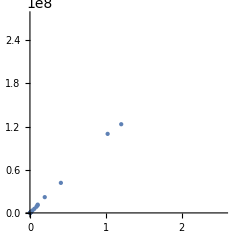

```mathematica
ListPlot[Transpose[{dataFF431Pi2DegreeLinearFront,dataFF4310DegreeLinearFront}],AspectRatio->1]
```

```mathematica
r = Total[(dataFF431Pi2DegreeLinearFront - Mean[dataFF431Pi2DegreeLinearFront]) (dataFF4310DegreeLinearFront - Mean[dataFF4310DegreeLinearFront])]/
    Sqrt[Total[(dataFF431Pi2DegreeLinearFront - Mean[dataFF431Pi2DegreeLinearFront])^2] Total[(dataFF4310DegreeLinearFront - Mean[dataFF4310DegreeLinearFront])^2]]
```

1.

```mathematica
N[Correlation[dataFF4310DegreeLinearFront,dataFF431Pi2DegreeLinearFront],20]
Correlation[dataFF4310DegreeLinearLat,dataFF431Pi2DegreeLinearLat]
Correlation[dataFF4310DegreeLinearRetro,dataFF431Pi2DegreeLinearRetro]
```

1.

0.668136

0.999697

```mathematica
fInterp541Linear = Interpolation[data541Linear,InterpolationOrder->1];

dataFF541Pi2DegreeLinearFront=Table[{fInterp541Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi/3,  Pi/60}];
dataFF541Pi2DegreeLinearLat=Table[{fInterp541Linear[th, Pi/2]/(4 Pi)}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF541Pi2DegreeLinearRetro=Table[{fInterp541Linear[th, Pi/2]/(4 Pi)}, {th, 2 Pi/3,  Pi,  Pi/60}];

dataFF5410DegreeLinearFront=Table[{fInterp541Linear[th, 0]/(4 Pi)}, {th, 0,  Pi/3,  Pi/60}];
dataFF5410DegreeLinearLat=Table[{fInterp541Linear[th, 0]/(4 Pi)}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF5410DegreeLinearRetro=Table[{fInterp541Linear[th, 0]/(4 Pi)}, {th, 2 Pi/3,  Pi,  Pi/60}];
```

```mathematica
Correlation[dataFF5410DegreeLinearFront,dataFF541Pi2DegreeLinearFront]
Correlation[dataFF5410DegreeLinearLat,dataFF541Pi2DegreeLinearLat]
Correlation[dataFF5410DegreeLinearRetro,dataFF541Pi2DegreeLinearRetro]
```

{{1.}}

{{0.499152}}

{{0.999226}}

```mathematica
fInterp573Linear = Interpolation[data573Linear,InterpolationOrder->1];

dataFF573Pi2DegreeLinearFront=Table[{fInterp573Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi/3,  Pi/60}];
dataFF573Pi2DegreeLinearLat=Table[{fInterp573Linear[th, Pi/2]/(4 Pi)}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF573Pi2DegreeLinearRetro=Table[{fInterp573Linear[th, Pi/2]/(4 Pi)}, {th, 2 Pi/3,  Pi,  Pi/60}];

dataFF5730DegreeLinearFront=Table[{fInterp573Linear[th, 0]/(4 Pi)}, {th, 0,  Pi/3,  Pi/60}];
dataFF5730DegreeLinearLat=Table[{fInterp573Linear[th, 0]/(4 Pi)}, {th, Pi/3, 2 Pi/3,  Pi/60}];
dataFF5730DegreeLinearRetro=Table[{fInterp573Linear[th, 0]/(4 Pi)}, {th, 2 Pi/3,  Pi,  Pi/60}];
```

```mathematica
Correlation[dataFF5730DegreeLinearFront,dataFF573Pi2DegreeLinearFront]
Correlation[dataFF5730DegreeLinearLat,dataFF573Pi2DegreeLinearLat]
Correlation[dataFF5730DegreeLinearRetro,dataFF573Pi2DegreeLinearRetro]
```

{{1.}}

{{0.70656}}

{{0.997843}}

#### Contribuciones integradas

```mathematica
CscaInt431Front0 = NIntegrate[(fInterp431Linear[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt431FrontPi2 = NIntegrate[(fInterp431Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt431FrontDif=100*Abs[CscaInt431Front0-CscaInt431FrontPi2]/CscaInt431Front0

CscaInt431Lat0 = NIntegrate[(fInterp431Linear[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt431LatPi2 = NIntegrate[(fInterp431Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt431LatDif=100*Abs[CscaInt431Lat0-CscaInt431LatPi2]/CscaInt431Lat0

CscaInt431Retro0 = NIntegrate[(fInterp431Linear[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt431RetroPi2 = NIntegrate[(fInterp431Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt431RetroDif=100*Abs[CscaInt431Retro0-CscaInt431RetroPi2]/CscaInt431Retro0
```

8.028×10^6

7.90145×10^6

1.57634

51736.5

95881.9

85.3274

8881.92

13114.1

47.6498

```mathematica
N[(Pi * 3750^2)]
```

4.41786×10^7

```mathematica
CscaInt431Front0/(Pi * 3750^2)
CscaInt431Lat0/(Pi * 3750^2)
CscaInt431Retro0/(Pi * 3750^2)

CscaInt431FrontPi2/(Pi * 3750^2)
CscaInt431LatPi2/(Pi * 3750^2)
CscaInt431RetroPi2/(Pi * 3750^2)
```

0.181717

0.00117107

0.000201046

0.178852

0.00217032

0.000296843

```mathematica
total0Eri=CscaInt431Front0+CscaInt431Lat0+CscaInt431Retro0;
CscaInt431Front0/total0Eri
CscaInt431Lat0/total0Eri
CscaInt431Retro0/total0Eri
```

0.992506

0.00639621

0.00109808

```mathematica
totalPi2Eri=CscaInt431FrontPi2+CscaInt431LatPi2+CscaInt431RetroPi2;
CscaInt431FrontPi2/totalPi2Eri
CscaInt431LatPi2/totalPi2Eri
CscaInt431RetroPi2/totalPi2Eri
```

0.986393

0.0119696

0.00163713

```mathematica
N[(Pi * 3750^2)]
```

4.41786×10^7

```mathematica
CscaInt541Front0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt541FrontPi2 = NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt541FrontDif=100*Abs[CscaInt541Front0-CscaInt541FrontPi2]/CscaInt541Front0


CscaInt541Lat0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt541LatPi2 = NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt541LatDif=100*Abs[CscaInt541Lat0-CscaInt541LatPi2]/CscaInt541Lat0


CscaInt541Retro0 = NIntegrate[(fInterp541Linear[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt541RetroPi2 = NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt541RetroDif=100*Abs[CscaInt541Retro0-CscaInt541RetroPi2]/CscaInt541Retro0
```

1.91037×10^7

1.89795×10^7

0.650345

66659.

92567.5

38.8671

47648.4

60836.2

27.6775

```mathematica
CscaInt541Front0/(Pi * 3750^2)
CscaInt541Lat0/(Pi * 3750^2)
CscaInt541Retro0/(Pi * 3750^2)

CscaInt541FrontPi2/(Pi * 3750^2)
CscaInt541LatPi2/(Pi * 3750^2)
CscaInt541RetroPi2/(Pi * 3750^2)
```

0.43242

0.00150885

0.00107854

0.429607

0.0020953

0.00137705

```mathematica
Abs[CscaInt541Front0/(Pi * 3750^2)-CscaInt541FrontPi2/(Pi * 3750^2)]
Abs[CscaInt541Lat0/(Pi * 3750^2)-CscaInt541LatPi2/(Pi * 3750^2)]
Abs[CscaInt541Retro0/(Pi * 3750^2)-CscaInt541RetroPi2/(Pi * 3750^2)]
```

0.00281222

0.000586446

0.000298512

```mathematica
CscaInt573Front0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, 0, Pi/3}]
CscaInt573FrontPi2 = NIntegrate[(fInterp573Linear[th,Pi/2]/(4 Pi))* Sin[th], {th, 0, Pi/3}]

CscaInt573FrontDif=100*Abs[CscaInt573Front0-CscaInt573FrontPi2]/CscaInt573Front0

CscaInt573Lat0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]
CscaInt573LatPi2 = NIntegrate[(fInterp573Linear[th, Pi/2]/(4 Pi))* Sin[th], {th, Pi/3, 2 Pi/3}]

CscaInt573LatDif=100*Abs[CscaInt573Lat0-CscaInt573LatPi2]/CscaInt573Lat0


CscaInt573Retro0 = NIntegrate[(fInterp573Linear[th, 0]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]
CscaInt573RetroPi2 = NIntegrate[(fInterp573Linear[th,Pi/2]/(4 Pi))* Sin[th], {th, 2 Pi/3,  Pi}]

CscaInt573RetroDif=100*Abs[CscaInt573Retro0-CscaInt573RetroPi2]/CscaInt573Retro0
```

2.05433×10^7

2.04389×10^7

0.508157

56327.8

111729.

98.3554

10872.

15076.5

38.6723

```mathematica
CscaInt573Front0/(Pi * 3750^2)
CscaInt573Lat0/(Pi * 3750^2)
CscaInt573Retro0/(Pi * 3750^2)

CscaInt573FrontPi2/(Pi * 3750^2)
CscaInt573LatPi2/(Pi * 3750^2)
CscaInt573RetroPi2/(Pi * 3750^2)
```

0.465005

0.001275

0.000246093

0.462642

0.00252903

0.000341262

```mathematica
Contribuciones integradas
```

#### Integracion experimental

```mathematica
resEri431=NIntegrate[
 (fInterp431Linear[th, phi]/(4 Pi))*
  Sin[th]*
  Boole[
    Abs[Sin[phi]] >= (2.2 Degree)/th
  ],
 {th, 2.2 Degree, 8.2 Degree},
 {phi, 0, 2 Pi},
 Method -> "LocalAdaptive"
]

resEri541=NIntegrate[
 (fInterp541Linear[th, phi]/(4 Pi))*
  Sin[th]*
  Boole[
    Abs[Sin[phi]] >= (2.2 Degree)/th
  ],
 {th, 2.2 Degree, 8.2 Degree},
 {phi, 0, 2 Pi},
 Method -> "LocalAdaptive"
]

resEri573=NIntegrate[
 (fInterp573Linear[th, phi]/(4 Pi))*
  Sin[th]*
  Boole[
    Abs[Sin[phi]] >= (2.2 Degree)/th
  ],
 {th, 2.2 Degree, 8.2 Degree},
 {phi, 0, 2 Pi},
 Method -> "LocalAdaptive"
]
```

9.13989×10^6

1.79155×10^7

1.93414×10^7

## lambda variadas

### Comparación con Papers

#### Skalak

```mathematica
dataSkalakCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Skalak_CST_FF_2.csv"];

dataThetaEriSanoSkalak=Drop[dataSkalakCSTFF,1][[All,1]];
dataPhiEriSanoSkalak=Drop[dataSkalakCSTFF,1][[All,2]];
dataRCSEriSanoSkalak=Drop[dataSkalakCSTFF,1][[All,3]];

data632 = Transpose[{dataThetaEriSanoSkalak *Pi/180, dataPhiEriSanoSkalak*Pi/180, dataRCSEriSanoSkalak}];
data632Linear = Transpose[{dataThetaEriSanoSkalak *Pi/180, dataPhiEriSanoSkalak*Pi/180, 10^(dataRCSEriSanoSkalak/10)}];
fInterp632 = Interpolation[data632,InterpolationOrder->1];
fInterp632Linear = Interpolation[data632Linear,InterpolationOrder->1];
min632 = Min[dataRCSEriSanoSkalak];
max632 = Max[dataRCSEriSanoSkalak];
```

```mathematica
dataSkalakpaper=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Skalak_paper.csv"];
datapaperSkalak=Interpolation[Transpose[{dataSkalakpaper[[All,1]],dataSkalakpaper[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplotSkalak=Table[{x,datapaperSkalak[x]},{x,0,180,0.05}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dataFF6320=Table[{th,fInterp632[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi,Pi/360}];
dataFF632Pi=Table[{th,fInterp632[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi,Pi/360}];
dataFF632Pi2=Table[{th,fInterp632[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF632Pi2Degree=Table[{th*180/Pi,fInterp632[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF632Pi2DegreeLinear=Table[{th*180/Pi,fInterp632Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF6320DegreeLinear=Table[{th*180/Pi,fInterp632Linear[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

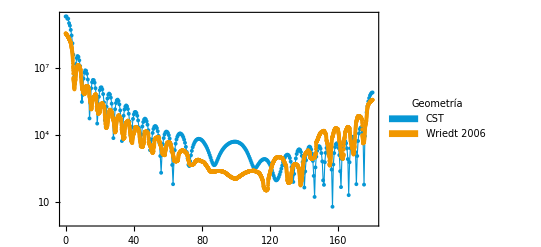

```mathematica
comparacionpaper=ListPlot[{dataFF632Pi2DegreeLinear,datapaperplotSkalak},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], 
                      Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]
                                                       &/@{"CST","Wriedt 2006","Tsin"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

#### Tsinopoulos

```mathematica
dataDSCSpaper=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\DSCS_paper.csv"];
datapaper=Interpolation[Transpose[{dataDSCSpaper[[All,1]],dataDSCSpaper[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplot=Table[{x,datapaper[x]},{x,0,180,0.5}];


dataDSCSpaper0=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\DSCS_paper_theta0.csv"];
datapaper0=Interpolation[Transpose[{dataDSCSpaper0[[All,1]],dataDSCSpaper0[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplot0=Table[{x,datapaper0[x]},{x,0,180,0.5}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {179.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180.} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
comparacionpaper=ListPlot[{dataFF4400DegreeLinear,datapaper},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[1]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\ \:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Tsinopoulos S., et al. 2002"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

ListPlot::lpn: {{},{{0.507519,23.3663},{1.69173,22.8943},{2.36842,22.2405},{2.87594,21.5503},{3.21429,20.7509},{3.38346,19.9879},{3.55263,19.2612},{3.7218,18.6435},{3.89098,17.626},{4.06015,13.12},«268»}} is not a list of numbers or pairs of numbers.

ListPlot[{dataFF4400DegreeLinear,InterpolatingFunction[…]},ScalingFunctions→Log,PlotMarkers→{●,4},Joined→True,PlotRange→{{Automatic,Automatic},{1.3,Automatic}},PlotStyle→{Directive[RGBColor[Rational[2, 85], Rational[151, 255], Rational[71, 85]],Thickness[0.002]],Directive[RGBColor[0.9, 0.36, 0.054],Thickness[0.002]]},FrameLabel→{{-Graphics-,None},{-Graphics-,None}},FrameTicks→{{Automatic,None},{Automatic,None}},PlotLegends→Placed[SwatchLegend[{CST,Tsinopoulos S., et al. 2002},LegendMarkerSize→{15,5},LegendLayout→{Column,1},LegendMargins→0,LegendLabel→Geometría,Spacings→0.05],{0.5,0.83}],ImagePadding→{{60,10},{60,50}},PlotRange→All,PlotStyle→{Directive[RGBColor[0., 0., 0.],Thickness[0.003]],Directive[RGBColor[0.3195368571428571, 0.1164, 0.4341454285714286],Thickness[0.003]],Directive[RGBColor[0.6695744285714286, 0.22438285714285713, 0.338128],Thickness[0.003]],Directive[RGBColor[0.8974812857142858, 0.3693308571428571, 0.1452665142857143],Thickness[0.003]],Directive[RGBColor[0.9882154285714286, 0.5505617142857143, 0.08483494285714285],Thickness[0.003]],Directive[RGBColor[1., 0.7397017142857143, 0.23300614285714283],Thickness[0.003]]},Frame→True,FrameStyle→Directive[GrayLevel[0],FontFamily→Latin Modern Roman 10,Magnification→1.8],LabelStyle→{FontFamily→Latin Modern Roman 10},ImagePadding→{{90,10},{70,10}}]

```mathematica
Export["paperComp.svg",comparacionpaper]
```

paperComp.svg

```mathematica
dataTsiCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Tsinopoulos_CST_FF_2.csv"];

dataThetaEriSanoTsi=Drop[dataTsiCSTFF,1][[All,1]];
dataPhiEriSanoTsi=Drop[dataTsiCSTFF,1][[All,2]];
dataRCSEriSanoTsi=Drop[dataTsiCSTFF,1][[All,3]];

data632Tsi = Transpose[{dataThetaEriSanoTsi *Pi/180, dataPhiEriSanoTsi*Pi/180, dataRCSEriSanoTsi}];
data632TsiLinear = Transpose[{dataThetaEriSanoTsi *Pi/180, dataPhiEriSanoTsi*Pi/180, 10^(dataRCSEriSanoTsi/10)}];
fInterp632Tsi = Interpolation[data632Tsi,InterpolationOrder->1];
fInterp632LinearTsi = Interpolation[data632TsiLinear,InterpolationOrder->1];
min632Tsi = Min[dataRCSEriSanoTsi];
max632Tsi = Max[dataRCSEriSanoTsi];
```

```mathematica
(*dataTsiCassCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Tsinopoulos_Cassini_CST_FF_2.csv"];*)
dataTsiCassCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Sano_Cassini_real.csv"];

dataThetaEriSanoTsiCass=Drop[dataTsiCassCSTFF,1][[All,1]];
dataPhiEriSanoTsiCass=Drop[dataTsiCassCSTFF,1][[All,2]];
dataRCSEriSanoTsiCass=Drop[dataTsiCassCSTFF,1][[All,3]];

data632TsiCass = Transpose[{dataThetaEriSanoTsiCass *Pi/180, dataPhiEriSanoTsiCass*Pi/180, dataRCSEriSanoTsiCass}];
data632TsiCassLinear = Transpose[{dataThetaEriSanoTsiCass *Pi/180, dataPhiEriSanoTsiCass*Pi/180, 10^(dataRCSEriSanoTsiCass/10)}];
fInterp632TsiCass = Interpolation[data632TsiCass,InterpolationOrder->1];
fInterp632LinearTsiCass = Interpolation[data632TsiCassLinear,InterpolationOrder->1];
```

```mathematica
dataSkalakpaper=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Skalak_paper.csv"];
datapaperSkalak=Interpolation[Transpose[{dataSkalakpaper[[All,1]],dataSkalakpaper[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplotSkalak=Table[{x,datapaperSkalak[x]},{x,0,180,0.05}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dataFF6320Tsi=Table[{th,fInterp632Tsi[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi,Pi/360}];
dataFF632PiTsi=Table[{th,fInterp632Tsi[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi,Pi/360}];
dataFF632Pi2Tsi=Table[{th,fInterp632Tsi[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF632Pi2DegreeTsi=Table[{th*180/Pi,fInterp632Tsi[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF632Pi2DegreeLinearTsi=Table[{th*180/Pi,fInterp632LinearTsi[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF6320DegreeLinearTsi=Table[{th*180/Pi,fInterp632LinearTsi[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

```mathematica
dataFF632Pi2DegreeTsiCass=Table[{th*180/Pi,fInterp632TsiCass[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF632Pi2DegreeLinearTsiCass=Table[{th*180/Pi,fInterp632LinearTsiCass[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF6320DegreeLinearTsiCass=Table[{th*180/Pi,fInterp632LinearTsiCass[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

```mathematica
Mean[Table[100*Abs[datapaper0[x]-(fInterp632LinearTsi[x*Pi/180,0]/(4 Pi))]/datapaper0[x],{x,0,180}]]
Mean[Table[100*Abs[datapaper[x]-(fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi))]/datapaper[x],{x,0,180}]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

84.9814

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

54.0498

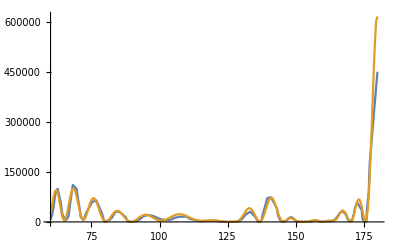

```mathematica
Plot[{datapaper[x],f632[x]},{x,60,180},PlotRange->All]
```

```mathematica
interv1=Table[{x, x + 5}, {x, 5, 90,5}];
interv2=Table[{x - 5, x + 5}, {x, 105, 174,10}]
intervals=Join[interv1,interv2]
```

{{100,110},{110,120},{120,130},{130,140},{140,150},{150,160},{160,170}}

{{5,10},{10,15},{15,20},{20,25},{25,30},{30,35},{35,40},{40,45},{45,50},{50,55},{55,60},{60,65},{65,70},{70,75},{75,80},{80,85},{85,90},{90,95},{100,110},{110,120},{120,130},{130,140},{140,150},{150,160},{160,170}}

```mathematica
f632[x_]:=fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi)
 locpaper=GoldenSearchMax[datapaper, #1, #2, 0.0005] & @@@ intervals
 locCST=GoldenSearchMax[f632, #1, #2, 0.0005] & @@@ intervals
 
 Mean[Abs[locpaper-locCST]]
```

```mathematica
f6320[x_]:=fInterp632LinearTsi[x*Pi/180,0]/(4 Pi)
 locpaper0=GoldenSearchMax[datapaper0, #1, #2, 0.0005] & @@@ intervals
 locCST0=GoldenSearchMax[f6320, #1, #2, 0.0005] & @@@ intervals
 
 Mean[Abs[locpaper0-locCST0]]
```

{5.65115,13.7952,17.618,21.4405,29.4183,33.0748,37.0635,41.2194,46.8699,51.8557,56.5094,62.6587,68.9748,70.0007,75.1249,80.0007,88.7537,90.0007,101.551,112.853,129.999,133.13,141.606,157.563,168.033}

{6.0001,13.9999,17.5003,21.5003,28.9999,33.4997,37.4997,42.,46.4995,51.0001,56.4995,62.,68.4997,70.0007,75.5004,80.0007,89.4996,90.0007,100.5,111.5,125.,133.5,141.499,156.5,167.5}

0.630358

```mathematica
Abs[datapaper0[50]-(fInterp632LinearTsi[50*Pi/180,0]/(4 Pi))]
```

```mathematica
fInterp632LinearTsi[50*Pi/180,0]/(4 Pi)
datapaper0[50]
```

39883.2

21681.8

```mathematica
datapaper0[0]
fInterp632LinearTsi[0*Pi/180,0]/(4 Pi)
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.44708×10^10

1.58778×10^10

```mathematica
Mean[Table[Abs[datapaper0[x]-(fInterp632LinearTsi[x*Pi/180,0]/(4 Pi))],{x,0,180}]]
Mean[Table[Abs[datapaper[x]-(fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi))],{x,0,180}]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

3.85032×10^7

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.85094×10^7

```mathematica
Mean[Table[Abs[datapaper0[x]-(fInterp632LinearTsi[x*Pi/180,0]/(4 Pi))]/datapaper0[x],{x,0,180}]]
Mean[Table[Abs[datapaper[x]-(fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi))]/datapaper[x],{x,0,180}]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.849814

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.540498

```mathematica
Correlation[dataFF632Pi2DegreeLinearTsi[[All,2]],datapaperplotPi2[[All,2]]]
Correlation[dataFF6320DegreeLinearTsi[[All,2]],datapaperplot0[[All,2]]]
```

0.996826

0.988327

```mathematica
Length[Range[0,180]]
```

```mathematica
RMSE=Sqrt[(1/181)*Total[Table[(datapaper0[x]-(fInterp632LinearTsi[x*Pi/180,0]/(4 Pi)))^2,{x,0,180}]]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

2.7308×10^8

```mathematica
NRMSE=RMSE/(Max[datapaperplot0]-Min[datapaperplot0])
```

0.0188711

```mathematica
NRMSE*100
```

1.88711

```mathematica
datapaperplot=Table[{x,datapaper[x]},{x,0,180,0.5}];


dataDSCSpaper0=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\DSCS_paper_theta0.csv"];
datapaper0=Interpolation[Transpose[{dataDSCSpaper0[[All,1]],dataDSCSpaper0[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplot0=Table[{x,datapaper0[x]},{x,0,180,0.05}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {179.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Length[dataFF632Pi2DegreeLinearTsi[[All,2]]]
```

361

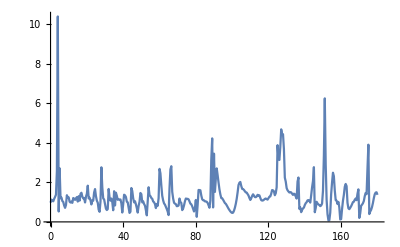

```mathematica
ListLinePlot[Transpose[{Range[0,180,0.5],dataFF632Pi2DegreeLinearTsi[[All,2]]/datapaperplot[[All,2]]}],PlotRange->All]
```

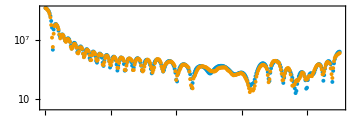

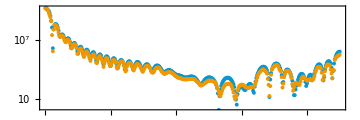

```mathematica
comparacionpaper90=ListPlot[{dataFF632Pi2DegreeLinearTsi,datapaperplot},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Tsinopoulos, S. V., et al. 2002"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.5,0.83}],
                      AspectRatio->1/3,
                      ImagePadding->{{90,10},{60,20}},
                      
                      Evaluate[Sequence @@ plotStyling]]
comparacionpaper0=ListPlot[{dataFF6320DegreeLinearTsi,datapaperplot0},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Tsinopoulos, S. V., et al. 2002"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.5,0.83}],
                     
                      ImagePadding->{{90,10},{60,60}},
                       AspectRatio->1/3,
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["comparacionpaper90.svg",comparacionpaper90]
Export["comparacionpaper0.svg",comparacionpaper0]
```

comparacionpaper90.svg

comparacionpaper0.svg

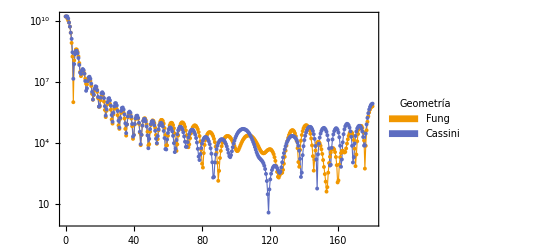

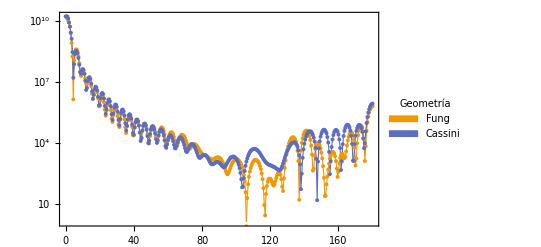

```mathematica
comparacionpaperCassini90=ListPlot[{dataFF632Pi2DegreeLinearTsi,dataFF632Pi2DegreeLinearTsiCass},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                       PlotRange->All,         
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"Fung","Cassini"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Joined->True,
                      Evaluate[Sequence @@ plotStyling]]
 
comparacionpaperCassini0=ListPlot[{dataFF6320DegreeLinearTsi,dataFF6320DegreeLinearTsiCass},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                       PlotRange->All,         
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"Fung","Cassini"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Joined->True,
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["comparacionpaperCassini90.svg",comparacionpaperCassini90]
Export["comparacionpaperCassini0.svg",comparacionpaperCassini0]
```

comparacionpaperCassini90.svg

comparacionpaperCassini0.svg

```mathematica
intervFront=Table[{x, x + 5}, {x, 5, 40,5}];
intervRetro=Table[{x, x + 5}, {x, 135, 175,5}];
intervLat=Table[{x - 5, x + 5}, {x, 50, 130,10}];
intervals=Join[intervFront,intervLat,intervRetro]
```

{{5,10},{10,15},{15,20},{20,25},{25,30},{30,35},{35,40},{40,45},{45,55},{55,65},{65,75},{75,85},{85,95},{95,105},{105,115},{115,125},{125,135},{135,140},{140,145},{145,150},{150,155},{155,160},{160,165},{165,170},{170,175},{175,180}}

```mathematica
cassini632[x_]:=fInterp632LinearTsiCass[x*Pi/180,Pi/2]/(4 Pi)
 cassiniMax=GoldenSearchMax[cassini632, #1, #2, 0.0005] & @@@ intervFront
 tsi632[x_]:=fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi)
 tsiMax=GoldenSearchMax[tsi632, #1, #2, 0.0005] & @@@ intervFront
 
 Mean[Abs[cassiniMax-tsiMax]]
```

{6.49947,13.9999,17.5003,21.5003,29.4996,33.4997,37.4997,42.}

{6.49947,13.9999,17.5003,21.5003,28.9999,33.4997,37.4997,42.}

0.0624624

```mathematica
cassini632[x_]:=fInterp632LinearTsiCass[x*Pi/180,Pi/2]/(4 Pi)
 cassiniMax=GoldenSearchMax[cassini632, #1, #2, 0.0005] & @@@ intervRetro
 tsi632[x_]:=fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi)
 tsiMax=GoldenSearchMax[tsi632, #1, #2, 0.0005] & @@@ intervRetro
 
 Mean[Abs[cassiniMax-tsiMax]]
```

{135.001,143.5,149.999,151.5,158.501,164.999,165.001,172.5,179.999}

{139.999,141.,148.,150.001,157.,162.5,167.5,173.,179.999}

1.99961

```mathematica
cassini632[x_]:=fInterp632LinearTsiCass[x*Pi/180,Pi/2]/(4 Pi)
 cassiniMax=GoldenSearchMax[cassini632, #1, #2, 0.0005] & @@@ intervRetro
 tsi632[x_]:=fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi)
 tsiMax=GoldenSearchMax[tsi632, #1, #2, 0.0005] & @@@ intervRetro
 
 Mean[Abs[cassiniMax-tsiMax]]
```

```mathematica
cassini632[x_]:=fInterp632LinearTsiCass[x*Pi/180,Pi/2]/(4 Pi)
 cassiniMax=GoldenSearchMax[cassini632, #1, #2, 0.0005] & @@@ intervLat
 tsi632[x_]:=fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi)
 tsiMax=GoldenSearchMax[tsi632, #1, #2, 0.0005] & @@@ intervLat
 
 Mean[Abs[cassiniMax-tsiMax]]
```

{50.9994,61.5002,67.4994,81.9999,91.9999,104.,105.001,122.501,132.999}

{51.0005,61.9999,68.4998,75.9996,94.9991,95.0009,107.999,120.,133.}

2.77777

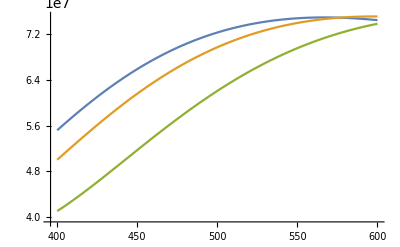

## Diferencia CST vs SolidWorks

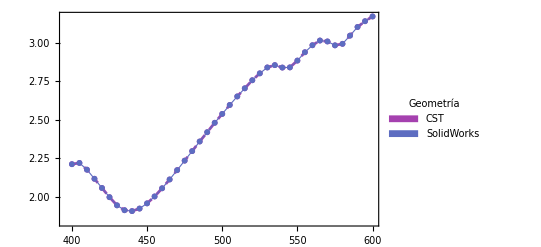

```mathematica
plotCSTSW=ListPlot[dataQext[dataQabsEsf[[#]],dataQscaEsf[[#]]]&/@{1,1},PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","SolidWorks"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.35,0.8}],
                      Joined->True,
                      PlotStyle -> {Directive[colors[[4]], Thickness[0.005],Dashed],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["CSTSW.svg",plotCSTSW]
```

CSTSW.svg

## Comparación

#### Contribuciones integradas en front, lat y retro

```mathematica
front0=Transpose[{{1,2,3},{CscaInt431Front0/(Pi * 3750^2)*10^1,CscaInt431Front0Esf/(Pi * 2680^2)*10^1,CscaInt431Front0Micro/(Pi * 3450^2)*10^1}}]
lat0=Transpose[{{1,2,3},{CscaInt431Lat0/(Pi * 3750^2)*10^(4),CscaInt431Lat0Esf/(Pi * 2680^2)*10^(4),CscaInt431Lat0Micro/(Pi * 3450^2)*10^(4)}}]
retro0=Transpose[{{1,2,3},{CscaInt431Retro0/(Pi * 3750^2)*10^(4),CscaInt431Retro0Esf/(Pi * 2680^2)*10^(4),CscaInt431Retro0Micro/(Pi * 3450^2)*10^(4)}}]
```

{{1,1.81717},{2,2.03046},{3,3.55707}}

{{1,11.7107},{2,7.60578},{3,11.5584}}

{{1,2.01046},{2,0.4725},{3,3.56588}}

```mathematica
mycolor1[x_] := If[Mod[x, 2] == 0,
   {colors[[9]],"●", 14},If[Mod[x, 3] == 0,
   {colors[[9]], "■", 18},{colors[[9]],"▲", 18}]];
mycolor2[x_] := If[Mod[x, 2] == 0,
   {colors[[10]],"●", 14},If[Mod[x, 3] == 0,
   {colors[[10]], "■", 18},{colors[[10]],"▲", 18}]];
mycolor3[x_] := If[Mod[x, 2] == 0,
   {colors[[11]],"●", 14},If[Mod[x, 3] == 0,
   {colors[[11]], "■", 18},{colors[[11]],"▲", 18}]];
```

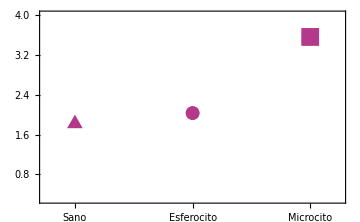

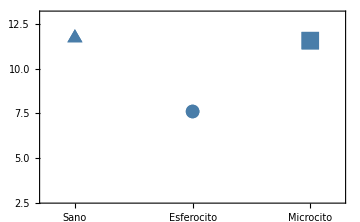

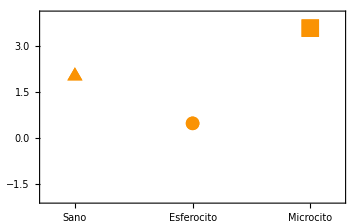

```mathematica
mycolorspec = mycolor1 /@ First /@ front0;
mycolorspec2 = mycolor2 /@ First /@ lat0;
mycolorspec3 = mycolor3 /@ First /@ retro0;
plot1=ListPlot[List /@ front0,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3,#1] &,
   mycolorspec, {1}], PlotRange->{{0.75,3.25},{0.3,4}},
                      PlotStyle -> Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],
                      FrameLabel->{{Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\times 10^{1}\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\mbox{Célula}"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{{{1, Style["Sano",Magnification->1.3]}, {2, Style["Esferocito",Magnification->1.3]},  
                                                                        {3, Style["Microcito",Magnification->1.3]}},None}},
                      ImageSize->Medium,
                      Evaluate[Sequence @@ plotStyling]]
   
 plot2=ListPlot[List /@ lat0,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3, #1] &,
   mycolorspec2, {1}], PlotRange->{{0.75,3.25},{2.7,13}},
                      PlotStyle -> Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],
                      FrameLabel->{{Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\times 10^{6}\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\mbox{Célula}"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{{{1, Style["Sano",Magnification->1.3]}, {2, Style["Esferocito",Magnification->1.3]},  
                                                                        {3, Style["Microcito",Magnification->1.3]}},None}},
                      ImageSize->Medium,
                      Evaluate[Sequence @@ plotStyling]]
   
plot3=ListPlot[List /@ retro0,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3, #1] &,
   mycolorspec3, {1}], PlotRange->{{0.75,3.25},{-2,4}},
                      PlotStyle -> Directive[RGBColor[85/255,153/255,1], Thickness[0.002]],
                      FrameLabel->{{Style[MaTeX["\\,\\text{d}C_{\\text{sca}}/\\text{d}\\Omega\\times 10^{6}\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\mbox{Célula}"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{{{1, Style["Sano",Magnification->1.3]}, {2, Style["Esferocito",Magnification->1.3]},  
                                                                        {3, Style["Microcito",Magnification->1.3]}},None}},
                      ImageSize->Medium,
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
list2
First /@ frontEri
```

{{1,1},{2,2},{3,3}}

{1,2,3}

```mathematica
frontlat0=Transpose[{{CscaInt431Front0/(Pi * 3750^2)*10^4,CscaInt431Front0Esf/(Pi * 2680^2)*10^4,CscaInt431Front0Micro/(Pi * 3450^2)*10^4},
                      {CscaInt431Lat0/(Pi * 3750^2)*10^(4),CscaInt431Lat0Esf/(Pi * 2680^2)*10^(4),CscaInt431Lat0Micro/(Pi * 3450^2)*10^(4)}}]
retro0={CscaInt431Retro0/(Pi * 3750^2)*10^(4),CscaInt431Retro0Esf/(Pi * 2680^2)*10^(4),CscaInt431Retro0Micro/(Pi * 3450^2)*10^(4)}


frontlatPi2=Transpose[{{CscaInt431FrontPi2/(Pi * 3750^2)*10^4,CscaInt431FrontPi2Esf/(Pi * 2680^2)*10^4,CscaInt431FrontPi2Micro/(Pi * 3450^2)*10^4},
                      {CscaInt431LatPi2/(Pi * 3750^2)*10^(4),CscaInt431LatPi2Esf/(Pi * 2680^2)*10^(4),CscaInt431LatPi2Micro/(Pi * 3450^2)*10^(4)}}]
retroPi2={CscaInt431RetroPi2/(Pi * 3750^2)*10^(4),CscaInt431RetroPi2Esf/(Pi * 2680^2)*10^(4),CscaInt431RetroPi2Micro/(Pi * 3450^2)*10^(4)}
```

{{1817.17,11.7107},{2030.46,7.60578},{3557.07,11.5584}}

{2.01046,0.4725,3.56588}

{{1788.52,21.7032},{2019.,14.4556},{3542.14,19.2113}}

{2.96843,0.90178,5.9973}

```mathematica
colorsCHCM
```

{RGBColor[0, Rational[2, 3], Rational[212, 255]],RGBColor[0, Rational[1, 5], Rational[128, 255]],RGBColor[Rational[11, 51], Rational[57, 85], Rational[40, 51]],RGBColor[1, Rational[14, 85], Rational[14, 85]],RGBColor[Rational[128, 255], 0, 0]}

```mathematica
mycolor0[x_] := If[Mod[x, CscaInt431Front0/(Pi * 3750^2)*10^4] == 0,
   {colorsCHCM[[1]],"●", 8.95},If[Mod[x, CscaInt431Front0Esf/(Pi * 2680^2)*10^4] == 0,
   {colorsCHCM[[4]], "●", 10},{colorsCHCM[[6]],"●", 17.52}]];
   
 mycolorPi2[x_] := If[Mod[x, CscaInt431FrontPi2/(Pi * 3750^2)*10^4] == 0,
   {colorsCHCM[[1]],"■", 8.86},If[Mod[x, CscaInt431FrontPi2Esf/(Pi * 2680^2)*10^4] == 0,
   {colorsCHCM[[4]], "■", 10},{colorsCHCM[[6]],"■", 17.54}]];
```

```mathematica
10*(CscaInt431FrontPi2Micro/(Pi * 3450^2)*10^4)/(CscaInt431FrontPi2Esf/(Pi * 2680^2)*10^4)
10*(CscaInt431FrontPi2/(Pi * 3750^2)*10^4)/(CscaInt431FrontPi2Esf/(Pi * 2680^2)*10^4)
```

17.544

8.85846

```mathematica
10*(CscaInt431Front0Micro/(Pi * 3450^2)*10^4)/(CscaInt431Front0Esf/(Pi * 2680^2)*10^4)
10*(CscaInt431Front0/(Pi * 3750^2)*10^4)/(CscaInt431Front0Esf/(Pi * 2680^2)*10^4)
```

17.5186

8.94954

```mathematica
First /@ frontlat0
```

{1817.17,2030.46,3557.07}

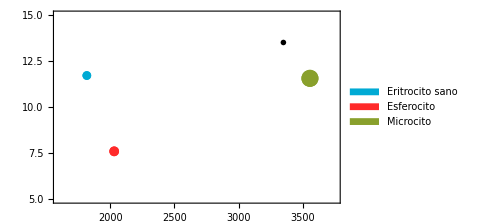

```mathematica
mycolorspec0 = mycolor0 /@ First /@ frontlat0;
plot0=ListPlot[List /@ frontlat0,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3,#1] &,
   mycolorspec0, {1}], PlotRange->{{1600,3750},{5,15}},
                      PlotStyle -> (Directive[#, Thickness[0.003]] & /@ {bluelight30,redlight34,greenlight30}),
                      FrameLabel->{{Style[MaTeX["\\,\\text{STL}\\times 10^{4}\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\text{STF}\\times 10^4\\,[\\text{nm}^2]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                      PlotLegends->Placed[SwatchLegend[{Style["Eritrocito sano",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                        Style["Esferocito",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                         Style["Microcito",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.25}],
                      Epilog -> Text[Style[MaTeX["\\varphi=0^{\\circ} "], Magnification->1.3],  {3350,13.5} ],
                      Evaluate[Sequence @@ plotStyling]]
```

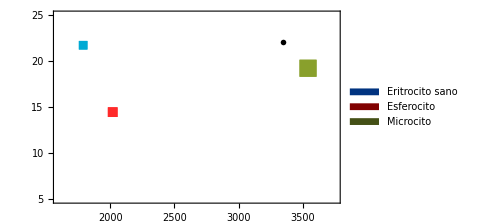

```mathematica
mycolorspecPi2 = mycolorPi2 /@ First /@ frontlatPi2;
plotPi2=ListPlot[List /@ frontlatPi2,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3,#1] &,
   mycolorspecPi2, {1}], PlotRange->{{1600,3750},{5,25}},
                      PlotStyle -> (Directive[#, Thickness[0.003]] & /@ {bluedark30,reddark34,greendark30}),
                      FrameLabel->{{Style[MaTeX["\\,\\text{STL}\\times 10^4\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\text{STF}\\times 10^4\\,[\\text{nm}^2]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                      Epilog -> Text[Style[MaTeX["\\varphi=90^{\\circ} "], Magnification->1.3],  {3350,22} ],
                      PlotLegends->Placed[SwatchLegend[{Style["Eritrocito sano",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                        Style["Esferocito",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                         Style["Microcito",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.25}],
                      Evaluate[Sequence @@ plotStyling]]
```

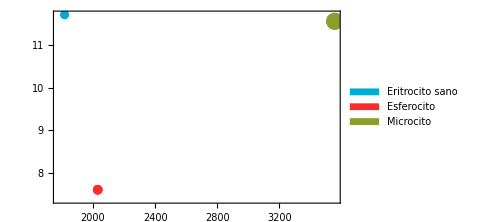

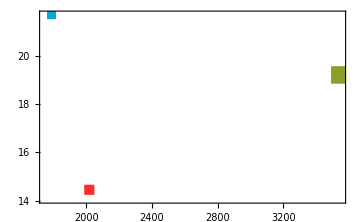

```mathematica
plot0=ListPlot[List /@ frontlat0,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3,#1] &,
   mycolorspec0, {1}], PlotRange->All,
                      PlotStyle -> (Directive[#, Thickness[0.003]] & /@ {bluelight30,redlight34,greenlight30}),
                      FrameLabel->"],Magnin->1.4],None},
                                {Style[MaTeX["\\text{STF}\\times 10^4\\,[\\text{nm}^2]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                                  PlotLegends->Placed[SwatchLegend[{Style["Eritrocito sano",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                        Style["Esferocito",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                         Style["Microcito",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.57,0.8}],
                      Evaluate[Sequence @@ plotStyling]]

plotPi2=ListPlot[List /@ frontlatPi2,
 PlotMarkers -> Apply[Style[#2, FontSize -> #3,#1] &,
   mycolorspecPi2, {1}], PlotRange->All,
                      PlotStyle -> (Directive[#, Thickness[0.003]] & /@ {bluedark30,reddark34,greendark30}),
                      FrameLabel->{{Style[MaTeX["\\,\\text{STL}\\times 10^4\\,[\\text{nm}^2] "],Magnification->1.4],None},
                                {Style[MaTeX["\\text{STF}\\times 10^4\\,[\\text{nm}^2]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      ImageSize->Medium,
                      Evaluate[Sequence @@ plotStyling]]
```

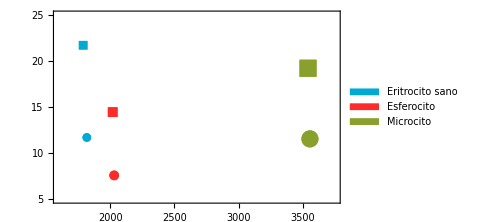

```mathematica
STLF0Pi2=Show[plot0,plotPi2,PlotRange->{{1600,3750},{5,25}}]
```

```mathematica
Export["STLF0Pi2.svg",STLF0Pi2]
```

STLF0Pi2.svg

```mathematica
Export["STLF0.svg",plot0]
Export["STLFPi2.svg",plotPi2]
```

STLF0.svg

STLFPi2.svg

#### Contribuciones integradas en tramos de theta: 431 nm. Pasos de 6

```mathematica
CscaInt431EriListPhi = Table[
   NIntegrate[(fInterp431Linear[th, phi * Degree]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0, 174, 6},{phi,0,90,10}
];
```

```mathematica
CscaInt431EsfListPhi = Table[
   NIntegrate[(fInterp431LinearEsf[th, phi * Degree]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0, 174, 6},{phi,0,90,10}
];

CscaInt431MicroListPhi = Table[
   NIntegrate[(fInterp431LinearMicro[th, phi * Degree]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0, 174, 6},{phi,0,90,10}
];
```

```mathematica
thetaVals = Range[0, 174, 6];
phiVals = Range[0, 90, 10];
```

```mathematica
NIntegrate[
   (fInterp431Linear[th, 90 Degree]/(4 Pi))*Sin[th],
   {th, 0, 6 Degree}
]
```

4.44184×10^6

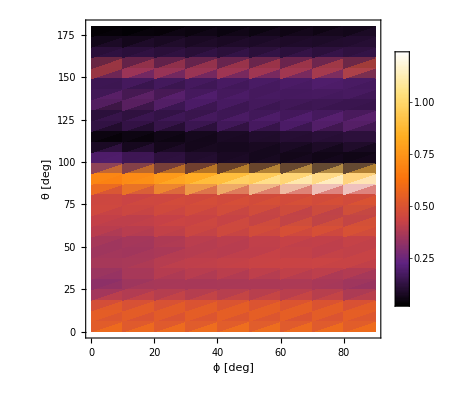

```mathematica
ListDensityPlot[CscaInt431EsfListPhi/CscaInt431EriListPhi,AxesLabel -> {"ϕ [deg]", "θ [deg]", "Integral"},
   ColorFunction -> "SunsetColors",PlotLegends->Automatic,
   DataRange -> {{0, 90}, {0, 180}},
   FrameLabel -> {Style[MaTeX["\\varphi\\,[\\text{deg}]"], Magnification -> 1.4], 
                 Style[MaTeX["\\theta\\,[\\text{deg}]"], Magnification -> 1.4]},
  FrameStyle -> Directive[Black, FontFamily -> "Latin Modern Roman 10", Magnification -> 1.6],
   Mesh -> None,
   ImagePadding->{{90,10},{60,20}}]
```

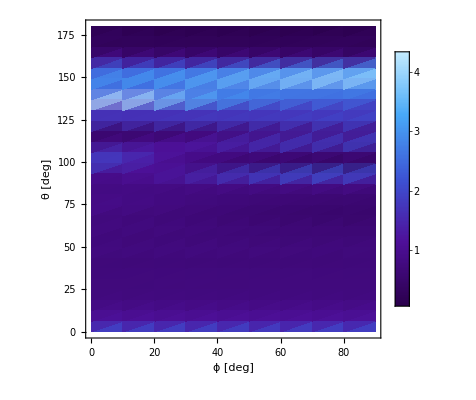

```mathematica
ListDensityPlot[CscaInt431MicroListPhi/CscaInt431EriListPhi,AxesLabel -> {"ϕ [deg]", "θ [deg]", "Integral"},
   ColorFunction -> "DeepSeaColors",PlotLegends->Automatic,
   DataRange -> {{0, 90}, {0, 180}},
   FrameLabel -> {Style[MaTeX["\\varphi\\,[\\text{deg}]"], Magnification -> 1.4], 
                 Style[MaTeX["\\theta\\,[\\text{deg}]"], Magnification -> 1.4]},
  FrameStyle -> Directive[Black, FontFamily -> "Latin Modern Roman 10", Magnification -> 1.6],
   Mesh -> None,
    ImagePadding->{{90,10},{60,20}}]
```

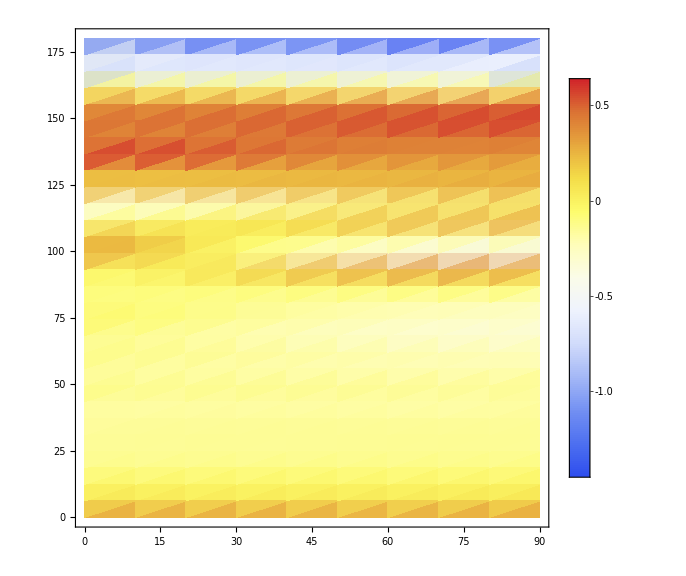

```mathematica
ListDensityPlot[
  (* Tus datos en logaritmo *)
  Log10[CscaInt431MicroListPhi/CscaInt431EriListPhi],
  
  (* --- LA SOLUCIÓN --- *)
  (* Le dice a la gráfica: "El eje X va de 0 a 90, y el eje Y va de 0 a 180" *)
  DataRange -> {{0, 90}, {0, 180}},
  
  (* El resto de tu formato *)
  ColorFunction -> "TemperatureMap",
  FrameLabel -> {Style[MaTeX["\\varphi\\,[\\text{deg}]"], Magnification -> 1.4], 
                 Style[MaTeX["\\theta\\,[\\text{deg}]"], Magnification -> 1.4]},
  FrameStyle -> Directive[Black, FontFamily -> "Latin Modern Roman 10", Magnification -> 1.6],
  PlotLegends -> Automatic,
  ImageSize -> Large
]
```

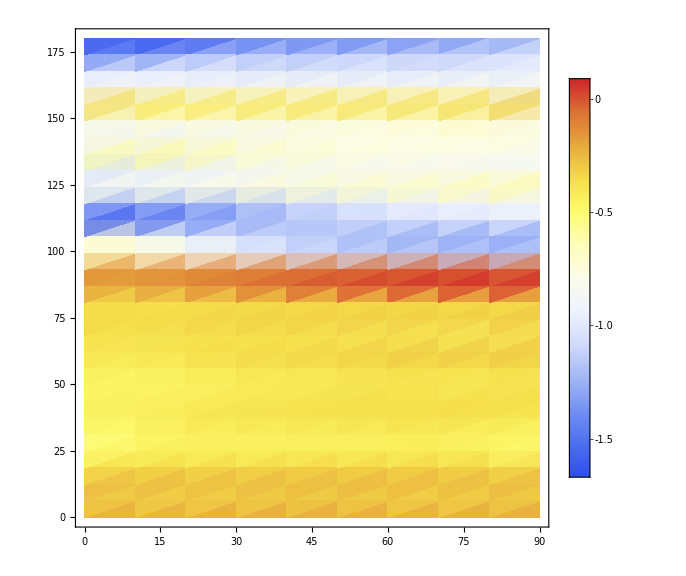

```mathematica
ListDensityPlot[
  (* Tus datos en logaritmo *)
  Log10[CscaInt431EsfListPhi/CscaInt431EriListPhi],
  
  (* --- LA SOLUCIÓN --- *)
  (* Le dice a la gráfica: "El eje X va de 0 a 90, y el eje Y va de 0 a 180" *)
  DataRange -> {{0, 90}, {0, 180}},
  
  (* El resto de tu formato *)
  ColorFunction -> "TemperatureMap",
  FrameLabel -> {Style[MaTeX["\\varphi\\,[\\text{deg}]"], Magnification -> 1.4], 
                 Style[MaTeX["\\theta\\,[\\text{deg}]"], Magnification -> 1.4]},
  FrameStyle -> Directive[Black, FontFamily -> "Latin Modern Roman 10", Magnification -> 1.6],
  PlotLegends -> Automatic,
  ImageSize -> Large
]
```

```mathematica
CscaInt431EriList0 = Table[
   NIntegrate[(fInterp431Linear[th, 0]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0, 174, 6}
];

CscaInt431EriListPi2 = Table[
   NIntegrate[(fInterp431Linear[th, Pi/2]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0, 174, 6}
];

CscaInt431EsfList0 = Table[
   NIntegrate[(fInterp431LinearEsf[th, 0]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0, 174, 6}
];

CscaInt431EsfListPi2 = Table[
   NIntegrate[(fInterp431LinearEsf[th, Pi/2]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0, 174, 6}
];

CscaInt431MicroList0 = Table[
   NIntegrate[(fInterp431LinearMicro[th, 0]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0, 174, 6}
];

CscaInt431MicroListPi2 = Table[
   NIntegrate[(fInterp431LinearMicro[th, Pi/2]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0, 174, 6}
];
```

```mathematica
Table[{i/6,i * Degree, (i + 6) * Degree},{i, 0, 174, 6}]
```

{{0,0,6 °},{1,6 °,12 °},{2,12 °,18 °},{3,18 °,24 °},{4,24 °,30 °},{5,30 °,36 °},{6,36 °,42 °},{7,42 °,48 °},{8,48 °,54 °},{9,54 °,60 °},{10,60 °,66 °},{11,66 °,72 °},{12,72 °,78 °},{13,78 °,84 °},{14,84 °,90 °},{15,90 °,96 °},{16,96 °,102 °},{17,102 °,108 °},{18,108 °,114 °},{19,114 °,120 °},{20,120 °,126 °},{21,126 °,132 °},{22,132 °,138 °},{23,138 °,144 °},{24,144 °,150 °},{25,150 °,156 °},{26,156 °,162 °},{27,162 °,168 °},{28,168 °,174 °},{29,174 °,180 °}}

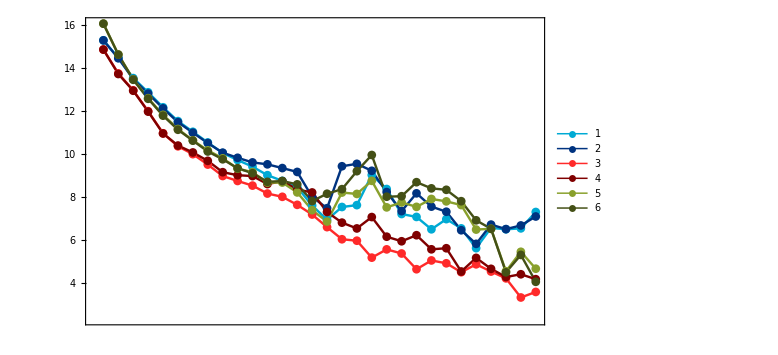

```mathematica
ListLinePlot[{Transpose[{Range[1,30],CscaInt431EriList0}],Transpose[{Range[1,30],CscaInt431EriListPi2}],
          Transpose[{Range[1,30],CscaInt431EsfList0}],Transpose[{Range[1,30],CscaInt431EsfListPi2}],
          Transpose[{Range[1,30],CscaInt431MicroList0}],Transpose[{Range[1,30],CscaInt431MicroListPi2}]},
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{bluelight30, bluedark30,redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.003]] & /@ {bluelight30, bluedark30,redlight34,reddark34,greenlight30,greendark30}),
          PlotLegends->Automatic,
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}\\,[\\text{nm}^2]"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
                               
          ImagePadding->{{90,10},{60,20}},
          FrameTicks->{{Automatic,None},{{{1, Style[MaTeX["6"],Magnification->1.3]},{2, Style[MaTeX["12"],Magnification->1.3]},
                                         {10, Style[MaTeX["54-60^{\\circ}"],Magnification->1.3]},  
                                                                        {20, Style[MaTeX["114-120^{\\circ}"],Magnification->1.3]}},None}},
          ImageSize->Large,
          Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Range[6,180,6]
```

{6,12,18,24,30,36,42,48,54,60,66,72,78,84,90,96,102,108,114,120,126,132,138,144,150,156,162,168,174,180}

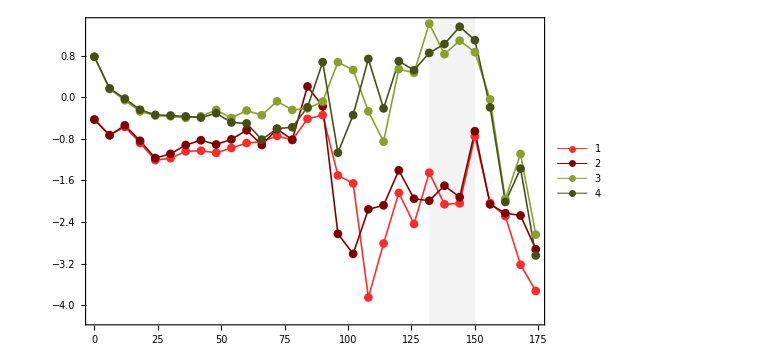

```mathematica
ListLinePlot[{Transpose[{Range[0,174,6],CscaInt431EsfList0/CscaInt431EriList0}],Transpose[{Range[0,174,6],CscaInt431EsfListPi2/CscaInt431EriListPi2}],
          Transpose[{Range[0,174,6],CscaInt431MicroList0/CscaInt431EriList0}],Transpose[{Range[0,174,6],CscaInt431MicroListPi2/CscaInt431EriListPi2}]},
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
          PlotLegends->Automatic,
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{sano}}/C_{\\text{sca}}^{\\text{enfermo}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
                               
          ImagePadding->{{90,10},{60,20}},
          
          ImageSize->Large,
          Prolog -> {
   FaceForm[Directive[LightGray, Opacity[0.3]]], 
   EdgeForm[Transparent], 
   (* X va de 21 a 26. Y va en escala Log10, por ejemplo de Log10[0.01] a Log10[1000] *)
   Rectangle[{132, -10}, {150, 5}]
},
          Evaluate[Sequence @@ plotStyling]]
```

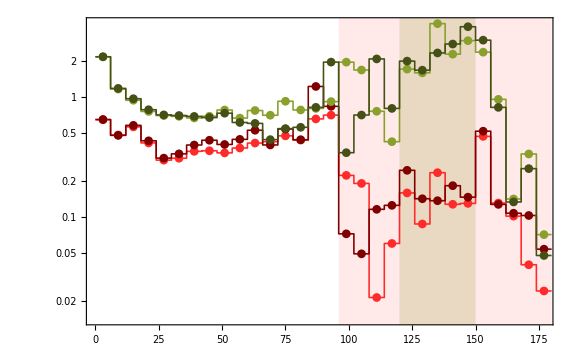

```mathematica
contriInt431=ListStepPlot[{Transpose[{Range[3,177,6],CscaInt431EsfList0/CscaInt431EriList0}],Transpose[{Range[3,177,6],CscaInt431EsfListPi2/CscaInt431EriListPi2}],
          Transpose[{Range[3,177,6],CscaInt431MicroList0/CscaInt431EriList0}],Transpose[{Range[3,177,6],CscaInt431MicroListPi2/CscaInt431EriListPi2}]},
          Center,
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito}(\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Esferocito}(\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito}(\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito}(\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.2}],
          ImageSize->Large,
          Prolog -> {
   {FaceForm[Directive[greenlight30, Opacity[0.2]]], 
   EdgeForm[Transparent], 
   (* X va de 21 a 26. Y va en escala Log10, por ejemplo de Log10[0.01] a Log10[1000] *)
   Rectangle[{120, -10}, {150, 5}],{FaceForm[Directive[redlight34, Opacity[0.1]]], 
   EdgeForm[Transparent], 
   (* X va de 21 a 26. Y va en escala Log10, por ejemplo de Log10[0.01] a Log10[1000] *)
   Rectangle[{96, -10}, {180, 5}]}
}},
          Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["contInt431.svg",contriInt431]
```

contInt431.svg

#### Contribuciones integradas en tramos de theta: 431 nm. Pasos de 1

```mathematica
CscaInt431EriList0 = Table[
   NIntegrate[(fInterp431Linear[th, 0]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt431EriListPi2 = Table[
   NIntegrate[(fInterp431Linear[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt431EsfList0 = Table[
   NIntegrate[(fInterp431LinearEsf[th, 0]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt431EsfListPi2 = Table[
   NIntegrate[(fInterp431LinearEsf[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt431MicroList0 = Table[
   NIntegrate[(fInterp431LinearMicro[th, 0]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt431MicroListPi2 = Table[
   NIntegrate[(fInterp431LinearMicro[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];
```

```mathematica
Back
```

```mathematica
hola1=Interpolation[Transpose[{Range[3,177,1],CscaInt431EsfList0/CscaInt431EriList0}]]
hola2=Interpolation[Transpose[{Range[3,177,1],CscaInt431EsfListPi2/CscaInt431EriListPi2}]]
hola3=Interpolation[Transpose[{Range[3,177,1],CscaInt431MicroList0/CscaInt431EriList0}]]
hola4=Interpolation[Transpose[{Range[3,177,1],CscaInt431MicroListPi2/CscaInt431EriListPi2}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

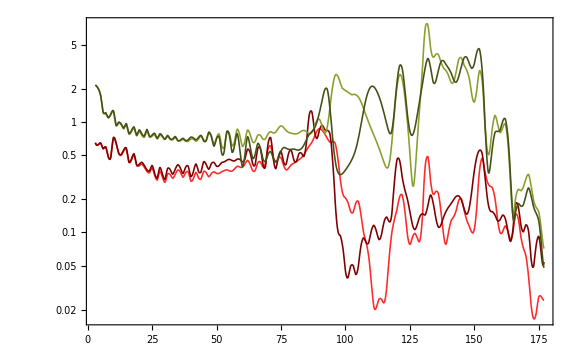

```mathematica
contriInt431Plot=Plot[{hola1[x],hola2[x],hola3[x],hola4[x]},{x,3,177},
     
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito}(\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Esferocito}(\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito}(\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito}(\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.2}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

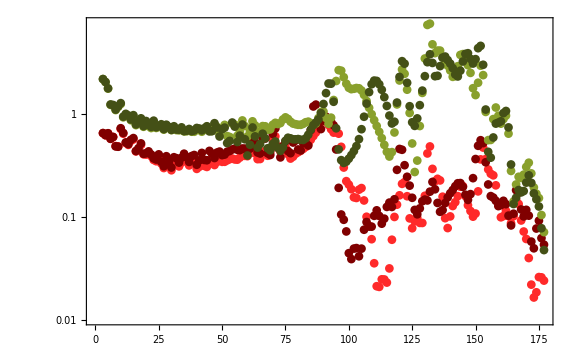

```mathematica
contriInt431List=ListPlot[{Transpose[{Range[3,177,1],CscaInt431EsfList0/CscaInt431EriList0}],Transpose[{Range[3,177,1],CscaInt431EsfListPi2/CscaInt431EriListPi2}],
          Transpose[{Range[3,177,1],CscaInt431MicroList0/CscaInt431EriList0}],Transpose[{Range[3,177,1],CscaInt431MicroListPi2/CscaInt431EriListPi2}]},
         
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          
       
          ImagePadding->{{90,10},{60,20}},

          ImageSize->Large,
             
            Evaluate[Sequence @@ plotStyling]]
```

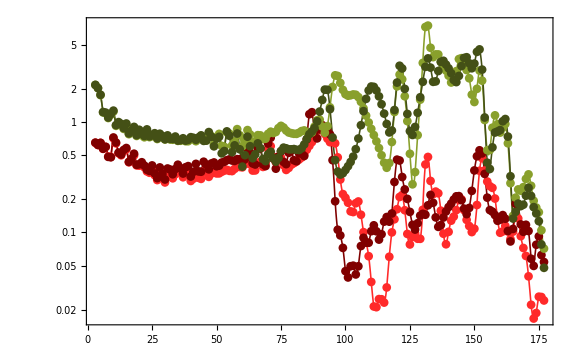

```mathematica
contriInt431=Show[contriInt431Plot,contriInt431List,PlotRange->All]
```

```mathematica
Export["contriInt431.svg",contriInt431]
```

contriInt431.svg

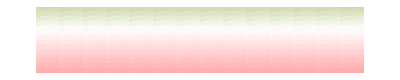

```mathematica
yMin = 0.01;
yMax = 10.0;
posBlanco = Rescale[Log[1.0], {Log[yMin], Log[yMax]}]; (* 2/3 *)

hola = DensityPlot[
   y, {x, 0, 180}, {y, Log[yMin], Log[yMax]},
   ColorFunction -> (
     Blend[
       {
         {0.0,       Lighter[redlight34, 0.6]},  (* {posición, color} *)
         {posBlanco, White},                     (* Blanco en 1.0 *)
         {1.0,       Lighter[greenlight30, 0.6]} (* Verde arriba *)
       },
       Rescale[#, {Log[yMin], Log[yMax]}]
     ] &
   ),
   ColorFunctionScaling -> False,
   PlotRangePadding -> None,
   Frame -> False,
   Axes -> False,
   AspectRatio -> Full
]
```

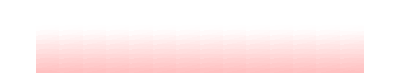

```mathematica
ymin = 0.008;
ymax = 10.1;

posBlanco = Rescale[Log[1.0], {Log[yMin], Log[yMax]}]; (* 2/3 *)

gradienteColorRojo431 = DensityPlot[
   y, {x, 0, 180}, {y, Log[yMin], Log[yMax]},
   ColorFunction -> (
     Blend[
       {
         {0.0,       Lighter[redlight34, 0.7]},  (* {posición, color} *)
         {posBlanco, White},                     (* Blanco en 1.0 *)
         {1.0,       White} (* Verde arriba *)
       },
       Rescale[#, {Log[yMin], Log[yMax]}]
     ] &
   ),
   ColorFunctionScaling -> False,
   PlotRangePadding -> None,
   Frame -> False,
   Axes -> False,
   AspectRatio -> Full
]
```

```mathematica
Export["gradienteColorRojo431.svg",gradienteColorRojo431]
```

gradienteColorRojo431.svg

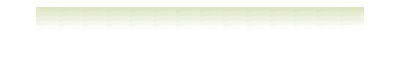

```mathematica
ymin = 0.008;
ymax = 10.1;

posBlanco = Rescale[Log[1.0], {Log[yMin], Log[yMax]}]; (* 2/3 *)

gradienteColorVerde431 = DensityPlot[
   y, {x, 0, 180}, {y, Log[yMin], Log[yMax]},
   ColorFunction -> (
     Blend[
       {
         {0.0,       White},  (* {posición, color} *)
         {posBlanco, White},                     (* Blanco en 1.0 *)
         {1.0,       Lighter[greenlight30, 0.7]} (* Verde arriba *)
       },
       Rescale[#, {Log[yMin], Log[yMax]}]
     ] &
   ),
   ColorFunctionScaling -> False,
   PlotRangePadding -> None,
   Frame -> False,
   Axes -> False,
   AspectRatio -> Full
]
```

```mathematica
Export["gradienteColorVerde431.svg",gradienteColorVerde431]
```

gradienteColorVerde431.svg

#### Contribuciones integradas en tramos de theta: 541 nm. Pasos de 6

```mathematica
CscaInt541EriList0 = Table[
   NIntegrate[(fInterp541Linear[th, 0]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0,174,6}
];

CscaInt541EriListPi2 = Table[
   NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i * Degree, (i + 6) * Degree}],
   {i, 0,174,6}
];

CscaInt541EsfList0 = Table[
   NIntegrate[(fInterp541LinearEsf[th, 0]/(4 Pi)) * Sin[th], {th,i * Degree, (i + 6) * Degree}],
   {i, 0,174,6}
];

CscaInt541EsfListPi2 = Table[
   NIntegrate[(fInterp541LinearEsf[th, Pi/2]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i, 0,174,6}
];

CscaInt541MicroList0 = Table[
   NIntegrate[(fInterp541LinearMicro[th, 0]/(4 Pi)) * Sin[th], {th, i * Degree, (i + 6) * Degree}],
   {i,0,174,6}
];

CscaInt541MicroListPi2 = Table[
   NIntegrate[(fInterp541LinearMicro[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 0,174,6}
];
```

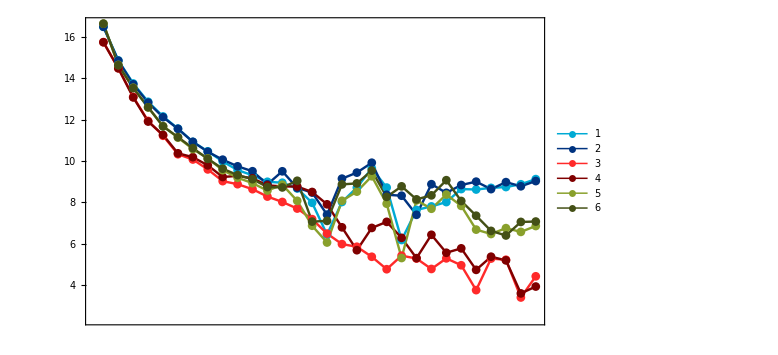

```mathematica
ListLinePlot[{Transpose[{Range[1,30],CscaInt541EriList0}],Transpose[{Range[1,30],CscaInt541EriListPi2}],
          Transpose[{Range[1,30],CscaInt541EsfList0}],Transpose[{Range[1,30],CscaInt541EsfListPi2}],
          Transpose[{Range[1,30],CscaInt541MicroList0}],Transpose[{Range[1,30],CscaInt541MicroListPi2}]},
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{bluelight30, bluedark30,redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.003]] & /@ {bluelight30, bluedark30,redlight34,reddark34,greenlight30,greendark30}),
          PlotLegends->Automatic,
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}\\,[\\text{nm}^2]"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
                               
          ImagePadding->{{90,10},{60,20}},
          FrameTicks->{{Automatic,None},{{{1, Style[MaTeX["6"],Magnification->1.3]},{2, Style[MaTeX["12"],Magnification->1.3]},
                                         {10, Style[MaTeX["54-60^{\\circ}"],Magnification->1.3]},  
                                                                        {20, Style[MaTeX["114-120^{\\circ}"],Magnification->1.3]}},None}},
          ImageSize->Large,
          Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Range[6,180,6]
```

{6,12,18,24,30,36,42,48,54,60,66,72,78,84,90,96,102,108,114,120,126,132,138,144,150,156,162,168,174,180}

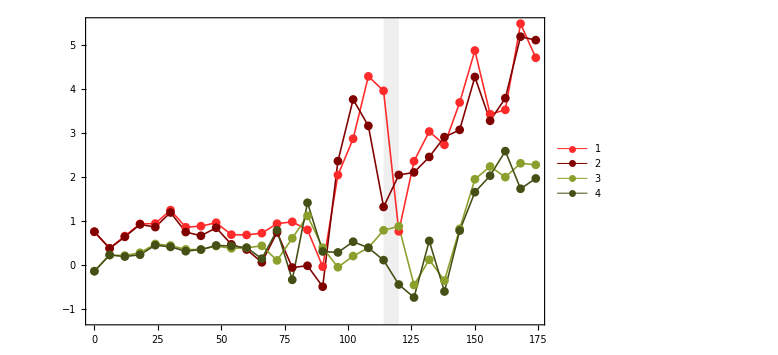

```mathematica
ListLinePlot[{Transpose[{Range[0,174,6],CscaInt541EriList0/CscaInt541EsfList0}],Transpose[{Range[0,174,6],CscaInt541EriListPi2/CscaInt541EsfListPi2}],
          Transpose[{Range[0,174,6],CscaInt541EriList0/CscaInt541MicroList0}],Transpose[{Range[0,174,6],CscaInt541EriListPi2/CscaInt541MicroListPi2}]},
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
          PlotLegends->Automatic,
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{sano}}/C_{\\text{sca}}^{\\text{enfermo}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
                               
          ImagePadding->{{90,10},{60,20}},
          
          ImageSize->Large,
          Prolog -> {
   FaceForm[Directive[LightGray, Opacity[0.4]]], 
   EdgeForm[Transparent], 
  
   Rectangle[{114, -2}, {120, 8}]
},
          Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Max[CscaInt541EriList0/CscaInt541EsfList0]
Min[CscaInt541EriList0/CscaInt541MicroList0]
```

239.072

0.629061

```mathematica
CscaInt541EriList0/CscaInt541EsfList0
CscaInt541EriList0/CscaInt541MicroList0
```

{2.10893,1.45068,1.91244,2.52619,2.54212,3.45157,2.34049,2.39803,2.59113,1.97584,1.96339,2.04479,2.53648,2.64508,2.204,0.953944,7.66096,17.4793,72.1688,51.8996,2.13135,10.4926,20.5981,15.2175,39.8695,129.835,30.561,33.7065,239.072,110.13}

{0.8617,1.24141,1.2267,1.30991,1.59858,1.54446,1.41295,1.40751,1.52504,1.44729,1.46505,1.53266,1.10055,1.82029,3.03058,1.4682,0.943327,1.21504,1.46793,2.18032,2.38879,0.629061,1.11869,0.695504,2.25295,6.95843,9.30577,7.3069,10.0069,9.6636}

```mathematica
Range[3,177,6]
```

{3,9,15,21,27,33,39,45,51,57,63,69,75,81,87,93,99,105,111,117,123,129,135,141,147,153,159,165,171,177}

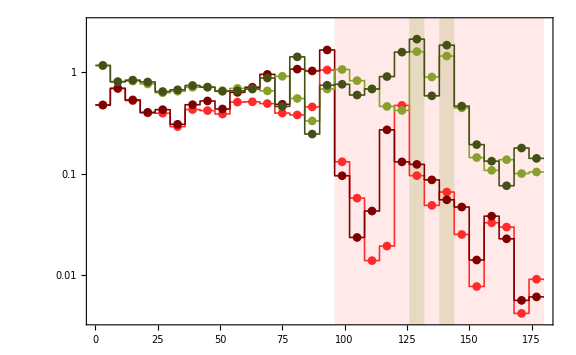

```mathematica
contriInt541=ListStepPlot[{Transpose[{Range[3,177,6],CscaInt541EsfList0/CscaInt541EriList0}],Transpose[{Range[3,177,6],CscaInt541EsfListPi2/CscaInt541EriListPi2}],
          Transpose[{Range[3,177,6],CscaInt541MicroList0/CscaInt541EriList0}],Transpose[{Range[3,177,6],CscaInt541MicroListPi2/CscaInt541EriListPi2}]},
          Center,
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
          
          PlotRange->{{Automatic,Automatic},{-1000,3}},
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
          PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito}(\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Esferocito}(\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito}(\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito}(\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.2}],
          ImageSize->Large,
          Prolog -> {
   {FaceForm[Directive[greenlight30, Opacity[0.2]]], 
   EdgeForm[Transparent], 
   (* X va de 21 a 26. Y va en escala Log10, por ejemplo de Log10[0.01] a Log10[1000] *)
   Rectangle[{138, -10}, {144, 5}],{FaceForm[Directive[redlight34, Opacity[0.1]]], 
   EdgeForm[Transparent], 
   (* X va de 21 a 26. Y va en escala Log10, por ejemplo de Log10[0.01] a Log10[1000] *)
   Rectangle[{96, -10}, {180, 5}]},
   {FaceForm[Directive[greenlight30, Opacity[0.2]]], 
   EdgeForm[Transparent], 
   (* X va de 21 a 26. Y va en escala Log10, por ejemplo de Log10[0.01] a Log10[1000] *)
   Rectangle[{126, -10}, {132, 5}]}
}},
          Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["contInt541.svg",contriInt541]
```

contInt541.svg

#### Contribuciones integradas en tramos de theta: 541 nm. Pasos de 1

```mathematica
CscaInt541EriList0 = Table[
   NIntegrate[(fInterp541Linear[th, 0]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt541EriListPi2 = Table[
   NIntegrate[(fInterp541Linear[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt541EsfList0 = Table[
   NIntegrate[(fInterp541LinearEsf[th, 0]/(4 Pi)) * Sin[th], {th,(i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt541EsfListPi2 = Table[
   NIntegrate[(fInterp541LinearEsf[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt541MicroList0 = Table[
   NIntegrate[(fInterp541LinearMicro[th, 0]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt541MicroListPi2 = Table[
   NIntegrate[(fInterp541LinearMicro[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];
```

```mathematica
int5410Esf=Interpolation[Transpose[{Range[3,177,1],CscaInt541EsfList0/CscaInt541EriList0}]]
int541Pi2Esf=Interpolation[Transpose[{Range[3,177,1],CscaInt541EsfListPi2/CscaInt541EriListPi2}]]
int5410Micro=Interpolation[Transpose[{Range[3,177,1],CscaInt541MicroList0/CscaInt541EriList0}]]
int541Pi2Micro=Interpolation[Transpose[{Range[3,177,1],CscaInt541MicroListPi2/CscaInt541EriListPi2}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

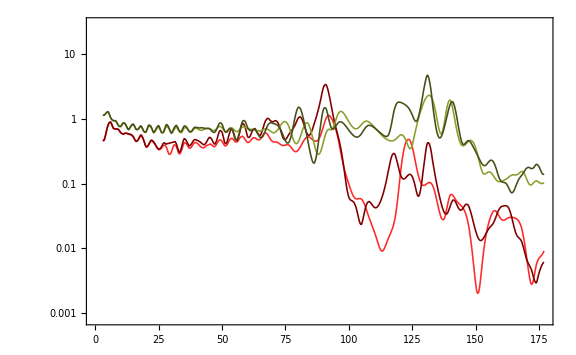

```mathematica
contriInt541Plot=Plot[{int5410Esf[x],int541Pi2Esf[x],int5410Micro[x],int541Pi2Micro[x]},{x,3,177},
     
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
         
          PlotRange->{{Automatic,Automatic},{0.0008,30}},
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito }(\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Esferocito }(\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito }(\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito }(\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.2}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

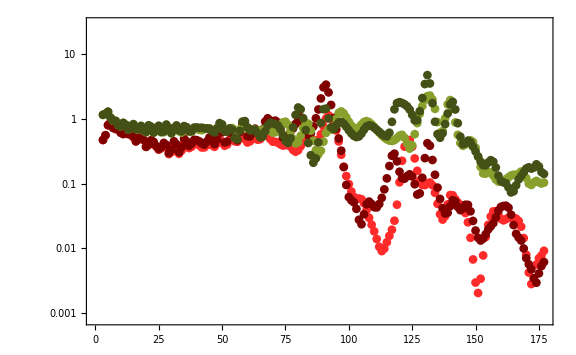

```mathematica
contriInt541List=ListPlot[{Transpose[{Range[3,177,1],CscaInt541EsfList0/CscaInt541EriList0}],Transpose[{Range[3,177,1],CscaInt541EsfListPi2/CscaInt541EriListPi2}],
          Transpose[{Range[3,177,1],CscaInt541MicroList0/CscaInt541EriList0}],Transpose[{Range[3,177,1],CscaInt541MicroListPi2/CscaInt541EriListPi2}]},
         
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
         
          PlotRange->{{Automatic,Automatic},{0.0008,30}},
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          
       
          ImagePadding->{{90,10},{60,20}},

          ImageSize->Large,
             
            Evaluate[Sequence @@ plotStyling]]
```

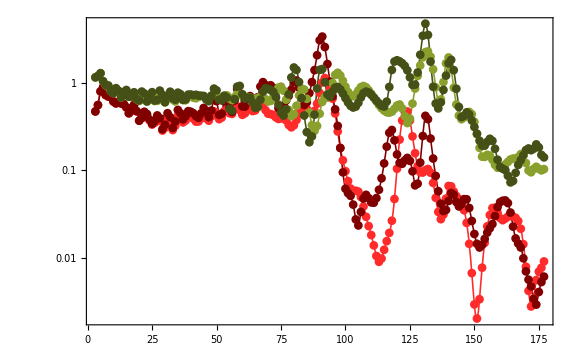

```mathematica
contriInt541=Show[contriInt541Plot,contriInt541List,PlotRange->{{Automatic,Automatic},{Automatic,3.3}}]
```

```mathematica
Export["contriInt541.svg",contriInt541]
```

contriInt541.svg

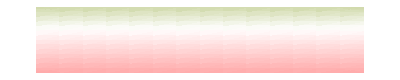

```mathematica
yMin541 = 0.0009;
yMax541 = 30;
posBlanco = Rescale[Log[1.0], {Log[yMin541], Log[yMax541]}]; (* 2/3 *)

hola = DensityPlot[
   y, {x, 0, 180}, {y, Log[yMin541], Log[yMax541]},
   ColorFunction -> (
     Blend[
       {
         {0.0,       Lighter[redlight34, 0.6]},  (* {posición, color} *)
         {posBlanco, White},                     (* Blanco en 1.0 *)
         {1.0,       Lighter[greenlight30, 0.6]} (* Verde arriba *)
       },
       Rescale[#, {Log[yMin541], Log[yMax541]}]
     ] &
   ),
   ColorFunctionScaling -> False,
   PlotRangePadding -> None,
   Frame -> False,
   Axes -> False,
   AspectRatio -> Full
]
```

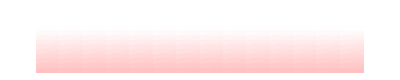

```mathematica
posBlanco = Rescale[Log[1.0], {Log[yMin541], Log[yMax541]}]; (* 2/3 *)

gradienteColorRojo541 = DensityPlot[
   y, {x, 0, 180}, {y, Log[yMin541], Log[yMax541]},
   ColorFunction -> (
     Blend[
       {
         {0.0,       Lighter[redlight34, 0.7]},  (* {posición, color} *)
         {posBlanco, White},                     (* Blanco en 1.0 *)
         {1.0,       White} (* Verde arriba *)
       },
       Rescale[#, {Log[yMin541], Log[yMax541]}]
     ] &
   ),
   ColorFunctionScaling -> False,
   PlotRangePadding -> None,
   Frame -> False,
   Axes -> False,
   AspectRatio -> Full
]
```

```mathematica
Export["gradienteColorRojo541.svg",gradienteColorRojo541]
```

gradienteColorRojo541.svg

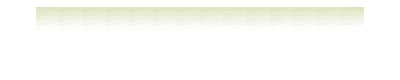

```mathematica
posBlanco = Rescale[Log[1.0], {Log[yMin541], Log[yMax541]}]; (* 2/3 *)

gradienteColorVerde541 = DensityPlot[
   y, {x, 0, 180}, {y, Log[yMin541], Log[yMax541]},
   ColorFunction -> (
     Blend[
       {
         {0.0,       White},  (* {posición, color} *)
         {posBlanco, White},                     (* Blanco en 1.0 *)
         {1.0,       Lighter[greenlight30, 0.7]} (* Verde arriba *)
       },
       Rescale[#, {Log[yMin541], Log[yMax541]}]
     ] &
   ),
   ColorFunctionScaling -> False,
   PlotRangePadding -> None,
   Frame -> False,
   Axes -> False,
   AspectRatio -> Full
]
```

```mathematica
Export["gradienteColorVerde541.svg",gradienteColorVerde541]
```

gradienteColorVerde541.svg

#### Contribuciones integradas en tramos de theta: 573 nm. Pasos de 1

```mathematica
CscaInt573EriList0 = Table[
   NIntegrate[(fInterp573Linear[th, 0]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3,177, 1}
];

CscaInt573EriListPi2 = Table[
   NIntegrate[(fInterp573Linear[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i,3,177, 1}
];

CscaInt573EsfList0 = Table[
   NIntegrate[(fInterp573LinearEsf[th, 0]/(4 Pi)) * Sin[th], {th,(i - 3) * Degree, (i + 3) * Degree}],
   {i, 3,177, 1}
];

CscaInt573EsfListPi2 = Table[
   NIntegrate[(fInterp573LinearEsf[th, Pi/2]/(4 Pi)) * Sin[th], {th,(i - 3) * Degree, (i + 3) * Degree}],
   {i, 3,177, 1}
];

CscaInt573MicroList0 = Table[
   NIntegrate[(fInterp573LinearMicro[th, 0]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3,177, 1}
];

CscaInt573MicroListPi2 = Table[
   NIntegrate[(fInterp573LinearMicro[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3,177, 1}
];
```

```mathematica
Export["contInt573.svg",contriInt573]
```

contInt573.svg

```mathematica
int5730Esf=Interpolation[Transpose[{Range[3,177,1],CscaInt573EsfList0/CscaInt573EriList0}]]
int573Pi2Esf=Interpolation[Transpose[{Range[3,177,1],CscaInt573EsfListPi2/CscaInt573EriListPi2}]]
int5730Micro=Interpolation[Transpose[{Range[3,177,1],CscaInt573MicroList0/CscaInt573EriList0}]]
int573Pi2Micro=Interpolation[Transpose[{Range[3,177,1],CscaInt573MicroListPi2/CscaInt573EriListPi2}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

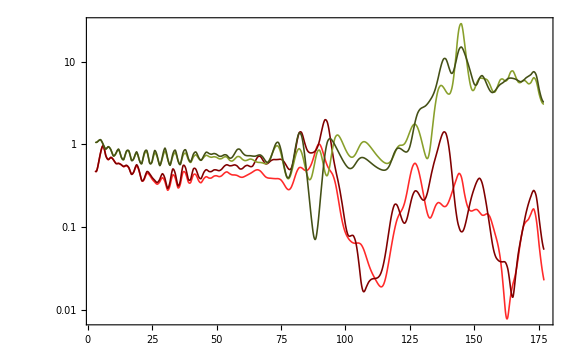

```mathematica
contriInt573Plot=Plot[{int5730Esf[x],int573Pi2Esf[x],int5730Micro[x],int573Pi2Micro[x]},{x,3,177},
     
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito }(\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Esferocito }(\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito }(\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito }(\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.2}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

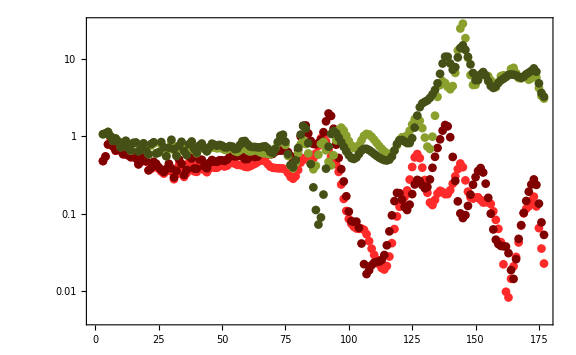

```mathematica
contriInt573List=ListPlot[{Transpose[{Range[3,177,1],CscaInt573EsfList0/CscaInt573EriList0}],Transpose[{Range[3,177,1],CscaInt573EsfListPi2/CscaInt573EriListPi2}],
          Transpose[{Range[3,177,1],CscaInt573MicroList0/CscaInt573EriList0}],Transpose[{Range[3,177,1],CscaInt573MicroListPi2/CscaInt573EriListPi2}]},
         
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          
       
          ImagePadding->{{90,10},{60,20}},

          ImageSize->Large,
             
            Evaluate[Sequence @@ plotStyling]]
```

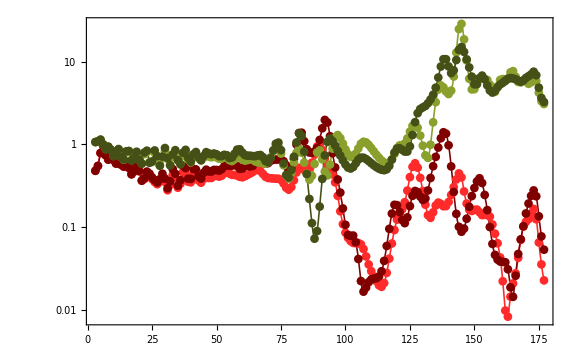

```mathematica
contriInt573=Show[contriInt573Plot,contriInt573List,PlotRange->All]
```

```mathematica
Export["contriInt573.svg",contriInt573]
```

contriInt573.svg

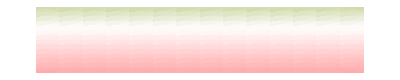

```mathematica
yMin573 = 0.004;
yMax573 = 12;
posBlanco = Rescale[Log[1.0], {Log[yMin573], Log[yMax573]}]; (* 2/3 *)

hola = DensityPlot[
   y, {x, 0, 180}, {y, Log[yMin573], Log[yMax573]},
   ColorFunction -> (
     Blend[
       {
         {0.0,       Lighter[redlight34, 0.6]},  (* {posición, color} *)
         {posBlanco, White},                     (* Blanco en 1.0 *)
         {1.0,       Lighter[greenlight30, 0.6]} (* Verde arriba *)
       },
       Rescale[#, {Log[yMin573], Log[yMax573]}]
     ] &
   ),
   ColorFunctionScaling -> False,
   PlotRangePadding -> None,
   Frame -> False,
   Axes -> False,
   AspectRatio -> Full
]
```

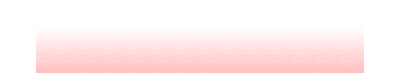

```mathematica
posBlanco = Rescale[Log[1.0], {Log[yMin573], Log[yMax573]}]; (* 2/3 *)

gradienteColorRojo573 = DensityPlot[
   y, {x, 0, 180}, {y, Log[yMin573], Log[yMax573]},
   ColorFunction -> (
     Blend[
       {
         {0.0,       Lighter[redlight34, 0.7]},  (* {posición, color} *)
         {posBlanco, White},                     (* Blanco en 1.0 *)
         {1.0,       White} (* Verde arriba *)
       },
       Rescale[#, {Log[yMin573], Log[yMax573]}]
     ] &
   ),
   ColorFunctionScaling -> False,
   PlotRangePadding -> None,
   Frame -> False,
   Axes -> False,
   AspectRatio -> Full
]
```

```mathematica
Export["gradienteColorRojo573.svg",gradienteColorRojo573]
```

gradienteColorRojo573.svg

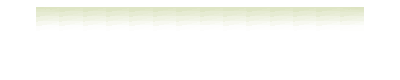

```mathematica
posBlanco = Rescale[Log[1.0], {Log[yMin573], Log[yMax573]}]; (* 2/3 *)

gradienteColorVerde573 = DensityPlot[
   y, {x, 0, 180}, {y, Log[yMin573], Log[yMax573]},
   ColorFunction -> (
     Blend[
       {
         {0.0,       White},  (* {posición, color} *)
         {posBlanco, White},                     (* Blanco en 1.0 *)
         {1.0,       Lighter[greenlight30, 0.7]} (* Verde arriba *)
       },
       Rescale[#, {Log[yMin573], Log[yMax573]}]
     ] &
   ),
   ColorFunctionScaling -> False,
   PlotRangePadding -> None,
   Frame -> False,
   Axes -> False,
   AspectRatio -> Full
]
```

```mathematica
Export["gradienteColorVerde573.svg",gradienteColorVerde573]
```

gradienteColorVerde573.svg

#### Contribuciones integradas en tramos de theta: 573 nm. Pasos de 6

```mathematica
CscaInt573EriList0 = Table[
   NIntegrate[(fInterp573Linear[th, 0]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3,177, 1}
];

CscaInt573EriListPi2 = Table[
   NIntegrate[(fInterp573Linear[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i,3,177, 1}
];

CscaInt573EsfList0 = Table[
   NIntegrate[(fInterp573LinearEsf[th, 0]/(4 Pi)) * Sin[th], {th,(i - 3) * Degree, (i + 3) * Degree}],
   {i, 3,177, 1}
];

CscaInt573EsfListPi2 = Table[
   NIntegrate[(fInterp573LinearEsf[th, Pi/2]/(4 Pi)) * Sin[th], {th,(i - 3) * Degree, (i + 3) * Degree}],
   {i, 3,177, 1}
];

CscaInt573MicroList0 = Table[
   NIntegrate[(fInterp573LinearMicro[th, 0]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3,177, 1}
];

CscaInt573MicroListPi2 = Table[
   NIntegrate[(fInterp573LinearMicro[th, Pi/2]/(4 Pi)) * Sin[th], {th, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3,177, 1}
];
```

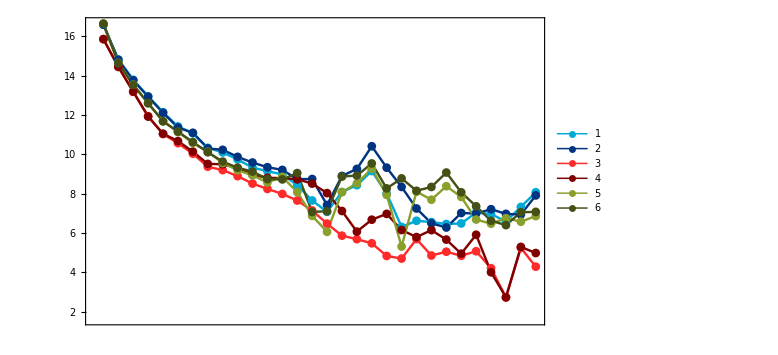

```mathematica
ListLinePlot[{Transpose[{Range[1,30],CscaInt573EriList0}],Transpose[{Range[1,30],CscaInt573EriListPi2}],
          Transpose[{Range[1,30],CscaInt573EsfList0}],Transpose[{Range[1,30],CscaInt573EsfListPi2}],
          Transpose[{Range[1,30],CscaInt573MicroList0}],Transpose[{Range[1,30],CscaInt573MicroListPi2}]},
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{bluelight30, bluedark30,redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.003]] & /@ {bluelight30, bluedark30,redlight34,reddark34,greenlight30,greendark30}),
          PlotLegends->Automatic,
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}\\,[\\text{nm}^2]"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
                               
          ImagePadding->{{90,10},{60,20}},
          FrameTicks->{{Automatic,None},{{{1, Style[MaTeX["6"],Magnification->1.3]},{2, Style[MaTeX["12"],Magnification->1.3]},
                                         {10, Style[MaTeX["54-60^{\\circ}"],Magnification->1.3]},  
                                                                        {20, Style[MaTeX["114-120^{\\circ}"],Magnification->1.3]}},None}},
          ImageSize->Large,
          Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Range[6,180,6]
```

{6,12,18,24,30,36,42,48,54,60,66,72,78,84,90,96,102,108,114,120,126,132,138,144,150,156,162,168,174,180}

```mathematica
ListLinePlot[{Transpose[{Range[0,180,6],CscaInt573EriList0/CscaInt573EsfList0}],Transpose[{Range[0,180,6],CscaInt573EriListPi2/CscaInt573EsfListPi2}],
          Transpose[{Range[0,180,6],CscaInt573EriList0/CscaInt573MicroList0}],Transpose[{Range[0,180,6],CscaInt573EriListPi2/CscaInt573MicroListPi2}]},
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
          PlotLegends->Automatic,
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{sano}}/C_{\\text{sca}}^{\\text{enfermo}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
                               
          ImagePadding->{{90,10},{60,20}},
          
          ImageSize->Large,
          Prolog -> {
   FaceForm[Directive[LightGray, Opacity[0.4]]], 
   EdgeForm[Transparent], 
  
   Rectangle[{114, -2}, {120, 8}]
},
          Evaluate[Sequence @@ plotStyling]]
```

Transpose::nmtx: The first two levels of {{0,6,12,18,24,30,36,42,48,54,«21»},{2.08363,1.44141,1.81909,2.74266,3.03208,2.34226,2.83151,2.61546,2.45459,2.34313,«20»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,6,12,18,24,30,36,42,48,54,«21»},{2.08738,1.43447,1.78761,2.74577,2.89119,1.98695,2.60499,2.20237,2.08028,1.77152,«20»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,6,12,18,24,30,36,42,48,54,«21»},{0.95051,1.18875,1.27694,1.4227,1.57501,1.32987,1.63666,1.22353,1.71194,1.73206,«20»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

-Graphics-

```mathematica
Max[CscaInt541EriList0/CscaInt541EsfList0]
Min[CscaInt541EriList0/CscaInt541MicroList0]
```

239.072

0.629061

```mathematica
CscaInt541EriList0/CscaInt541EsfList0
CscaInt541EriList0/CscaInt541MicroList0
```

{2.10893,1.45068,1.91244,2.52619,2.54212,3.45157,2.34049,2.39803,2.59113,1.97584,1.96339,2.04479,2.53648,2.64508,2.204,0.953944,7.66096,17.4793,72.1688,51.8996,2.13135,10.4926,20.5981,15.2175,39.8695,129.835,30.561,33.7065,239.072,110.13}

{0.8617,1.24141,1.2267,1.30991,1.59858,1.54446,1.41295,1.40751,1.52504,1.44729,1.46505,1.53266,1.10055,1.82029,3.03058,1.4682,0.943327,1.21504,1.46793,2.18032,2.38879,0.629061,1.11869,0.695504,2.25295,6.95843,9.30577,7.3069,10.0069,9.6636}

```mathematica
Range[3,177,6]
```

{3,9,15,21,27,33,39,45,51,57,63,69,75,81,87,93,99,105,111,117,123,129,135,141,147,153,159,165,171,177}

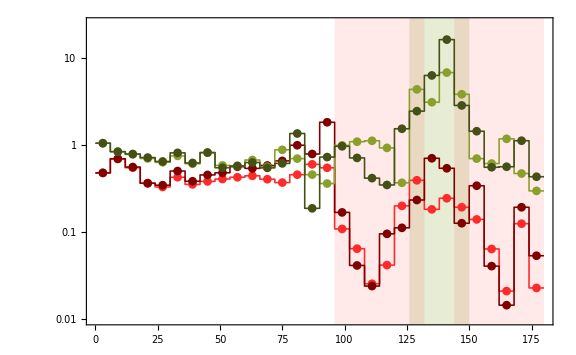

```mathematica
contriInt573=ListStepPlot[{Transpose[{Range[3,177,6],CscaInt573EsfList0/CscaInt573EriList0}],Transpose[{Range[3,177,6],CscaInt573EsfListPi2/CscaInt573EriListPi2}],
          Transpose[{Range[3,177,6],CscaInt573MicroList0/CscaInt573EriList0}],Transpose[{Range[3,177,6],CscaInt573MicroListPi2/CscaInt573EriListPi2}]},
          Center,
          PlotMarkers -> (Style["●", FontSize -> 8.95,#]&/@{redlight34,reddark34,greenlight30,greendark30}),
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34,greenlight30,greendark30}),
         
          PlotRange->{{Automatic,Automatic},{0.01,25}},
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
          PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito} (\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Esferocito} (\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito} (\\varphi=0^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style[MaTeX["\\text{Microcito} (\\varphi=90^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.2}],
          ImageSize->Large,
          Prolog -> {
   {FaceForm[Directive[greenlight30, Opacity[0.2]]], 
   EdgeForm[Transparent], 
   (* X va de 21 a 26. Y va en escala Log10, por ejemplo de Log10[0.01] a Log10[1000] *)
   Rectangle[{126, -10}, {150, 5}]},{FaceForm[Directive[redlight34, Opacity[0.1]]], 
   EdgeForm[Transparent], 
   Rectangle[{96, -10}, {132, 5}]},
   {FaceForm[Directive[redlight34, Opacity[0.1]]], 
   EdgeForm[Transparent], 
   Rectangle[{144, -10}, {180, 5}]}
},
          Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["contInt573.svg",contriInt573]
```

contInt573.svg

#### Contribuciones integradas en tramos de phi: 431 nm. Pasos de 1

```mathematica
CscaInt431EriList135 = Table[
   NIntegrate[(fInterp431Linear[130* Degree, ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}];

CscaInt431EsfList135= Table[
   NIntegrate[(fInterp431LinearEsf[130* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt431MicroList135 = Table[
   NIntegrate[(fInterp431LinearMicro[130* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];
```

```mathematica
CscaInt431Esf135=Interpolation[Transpose[{Range[3,177,1],CscaInt431EsfList/CscaInt431EriList}]]
CscaInt431Micro135=Interpolation[Transpose[{Range[3,177,1],CscaInt431MicroList/CscaInt431EriList}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

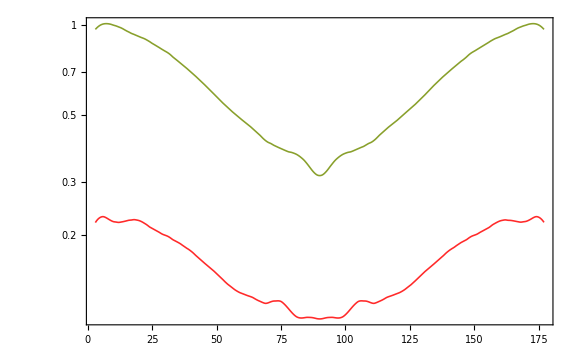

```mathematica
contriInt431PlotPhi=Plot[{CscaInt431Esf[x],CscaInt431Micro[x]},{x,3,177},
     
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,greenlight30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\varphi\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito }(\\theta=135^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                             
                                                Style[MaTeX["\\text{Microcito }(\\theta=135^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]
                                                },
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.7}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["contriInt431.svg",contriInt431]
```

contriInt431.svg

```mathematica
CscaInt431EriList130 = Table[
   NIntegrate[(fInterp431Linear[130* Degree, ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}];

CscaInt431EsfList130= Table[
   NIntegrate[(fInterp431LinearEsf[130* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt431MicroList130 = Table[
   NIntegrate[(fInterp431LinearMicro[130* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];
```

```mathematica
CscaInt431Esf130=Interpolation[Transpose[{Range[3,177,1],CscaInt431EsfList130/CscaInt431EriList130}]];
CscaInt431Micro130=Interpolation[Transpose[{Range[3,177,1],CscaInt431MicroList130/CscaInt431EriList130}]];
```

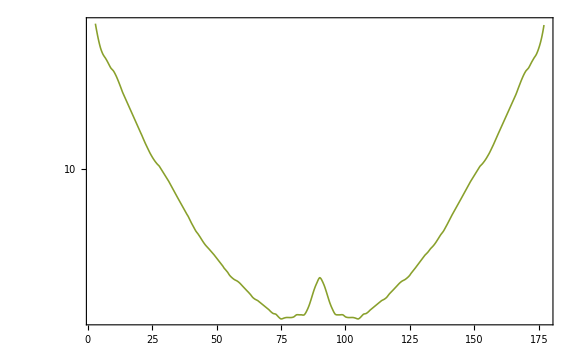

```mathematica
contriInt431PlotPhi=Plot[{CscaInt431Micro130[x]},{x,3,177},
     
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,greenlight30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\varphi\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito }(\\theta=135^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                             
                                                Style[MaTeX["\\text{Microcito }(\\theta=135^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]
                                                },
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.7}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

```mathematica
CscaInt431EriList140 = Table[
   NIntegrate[(fInterp431Linear[140* Degree, ph]/(4 Pi)) * Sin[140* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}];

CscaInt431EsfList140= Table[
   NIntegrate[(fInterp431LinearEsf[140* Degree,ph]/(4 Pi)) * Sin[140* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt431MicroList140 = Table[
   NIntegrate[(fInterp431LinearMicro[140* Degree,ph]/(4 Pi)) * Sin[140* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];
```

```mathematica
CscaInt431EriList120 = Table[
   NIntegrate[(fInterp431Linear[120* Degree, ph]/(4 Pi)) * Sin[120* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}];

CscaInt431EsfList120= Table[
   NIntegrate[(fInterp431LinearEsf[120* Degree,ph]/(4 Pi)) * Sin[120* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt431MicroList120 = Table[
   NIntegrate[(fInterp431LinearMicro[120* Degree,ph]/(4 Pi)) * Sin[120* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];
```

```mathematica
CscaInt431Esf120=Interpolation[Transpose[{Range[3,177,1],CscaInt431EsfList120/CscaInt431EriList120}]];
CscaInt431Micro120=Interpolation[Transpose[{Range[3,177,1],CscaInt431MicroList120/CscaInt431EriList120}]];
```

```mathematica
CscaInt431Esf140=Interpolation[Transpose[{Range[3,177,1],CscaInt431EsfList140/CscaInt431EriList140}]];
CscaInt431Micro140=Interpolation[Transpose[{Range[3,177,1],CscaInt431MicroList140/CscaInt431EriList140}]];
```

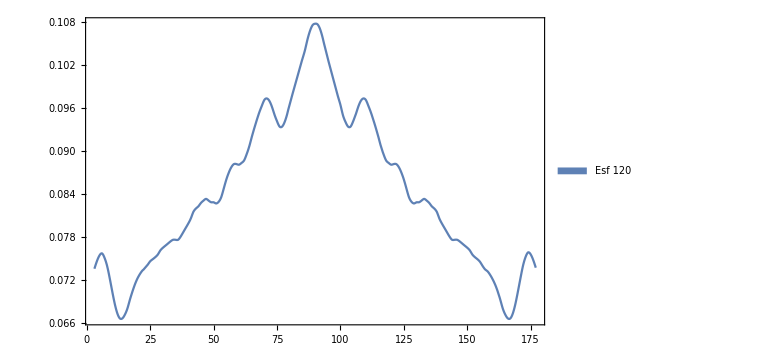

```mathematica
contriInt431PlotPhi130=Plot[{CscaInt431Esf140[x]},{x,3,177},
     
           
         PlotStyle->Automatic,
         PlotRange -> All,
          
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\varphi\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{"Esf 120", "Micro 120", "Esf 130", "Micro 130","Esf 140", "Micro 140"
                                                },
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.5,0.5}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

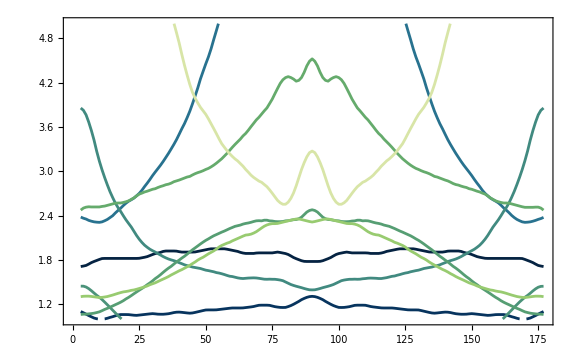

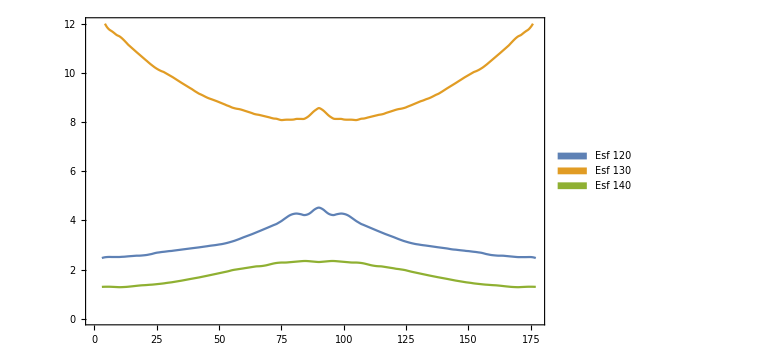

```mathematica
contriInt431PlotPhi130=Plot[{CscaInt431Micro120[x],
CscaInt431Micro130[x],CscaInt431Micro140[x]},{x,3,177},
     
           
         PlotStyle->Automatic,
         PlotRange -> {{Automatic,Automatic},{0,12}},
          
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\varphi\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{"Esf 120", "Esf 130", "Esf 140", "Micro 140"
                                                },
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.5,0.5}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["contriInt431PlotPhi130.svg",contriInt431PlotPhi130]
```

contriInt431PlotPhi130.svg

```mathematica
CscaInt431EriTheta = Table[
   {
    th,
    Table[
     NIntegrate[
      (fInterp431Linear[th Degree, ph]/(4 Pi)) Sin[th Degree],
      {ph, (i - 3) Degree, (i + 3) Degree}
      ],
     {i, 3, 177, 1}
     ]
    },
   {th, 0, 180,10}
   ];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
CscaInt431EsfTheta = Table[
   {
    th,
    Table[
     NIntegrate[
      (fInterp431LinearEsf[th Degree, ph]/(4 Pi)) Sin[th Degree],
      {ph, (i - 3) Degree, (i + 3) Degree}
      ],
     {i, 3, 177, 1}
     ]
    },
   {th, 0, 180, 10}
   ];
```

```mathematica
CscaInt431MicroTheta = Table[
   {
    th,
    Table[
     NIntegrate[
      (fInterp431LinearMicro[th Degree, ph]/(4 Pi)) Sin[th Degree],
      {ph, (i - 3) Degree, (i + 3) Degree}
      ],
     {i, 3, 177, 1}
     ]
    },
   {th, 0, 180, 10}
   ];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
ratioEsfEriTheta = Table[
   {
    CscaInt431EriTheta[[j, 1]],
    CscaInt431EsfTheta[[j, 2]]/
     CscaInt431EriTheta[[j, 2]]
    },
   {j, 2, Length[CscaInt431EriTheta]-1}
   ];
```

```mathematica
ratioMicroEriTheta = Table[
   {
    CscaInt431EriTheta[[j, 1]],
    CscaInt431MicroTheta[[j, 2]]/
     CscaInt431EriTheta[[j, 2]]
    },
   {j, 2, Length[CscaInt431EriTheta]-1}
   ];
```

```mathematica
phiValues = Range[3, 177];
```

```mathematica
cfThetaEsf = ColorMapSuite["lajolla"];
```

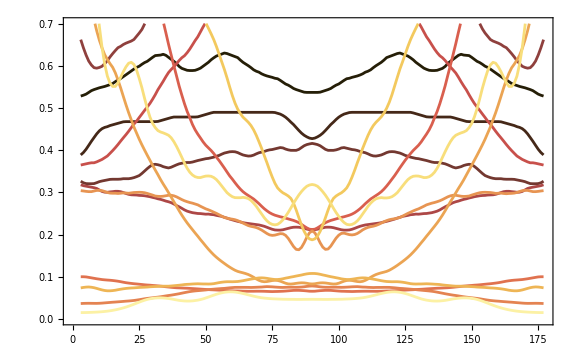

```mathematica
plotRatioEsfEri = ListLinePlot[
  Table[
   Transpose[{phiValues, ratioEsfEriTheta[[j, 2]]}],
   {j, 1, Length[ratioEsfEriTheta]}
  ],

  PlotStyle -> Table[
    Directive[
      cfThetaEsf[
        Rescale[
          ratioEsfEriTheta[[j, 1]],
          {0, 180}
        ]
      ],
      AbsoluteThickness[2]
    ],
    {j, 1, Length[ratioEsfEriTheta]}
  ],

  PlotRange -> {{Automatic,Automatic},{0,0.7}},
  Frame -> True,
  Axes -> False,

  FrameLabel -> {
    Style[
      MaTeX["\\varphi\\,[\\text{deg}]"],
      Magnification -> 1.4
    ],
    Style[
      MaTeX["C_{\\text{sca}}^{\\text{eritrocito}}/C_{\\text{sca}}^{\\text{sano}}"
      ],
      Magnification -> 1.4
    ]
  },
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10"],
  PlotLegends -> BarLegend[
    {cfThetaEsf, {0, 180}},
    Ticks -> (
      {#, NumberForm[#, {3, 0}]} & /@
       Range[0, 180, 30]
    ),
    LegendLabel ->
      Style[
        MaTeX["\\theta\\,[\\text{deg}]"],
        Magnification -> 1.4
      ]
  ],

  LabelStyle -> {
    Black,
    FontFamily -> "Latin Modern Roman 10",
    FontSize -> 18
  },

  ImageSize -> Large
]
```

```mathematica
Export["plotRatioEsfEri.svg",plotRatioEsfEri]
```

plotRatioEsfEri.svg

```mathematica
cfThetaMicro = ColorMapSuite["navia"];
```

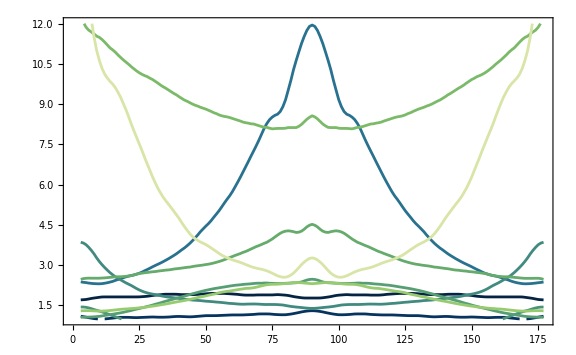

```mathematica
plotRatioMicroEri = ListLinePlot[
  Table[
   Transpose[{phiValues, ratioMicroEriTheta[[j, 2]]}],
   {j, 1, Length[ratioEsfEriTheta]}
  ],

  PlotStyle -> Table[
    Directive[
      cfThetaMicro[
        Rescale[
          ratioMicroEriTheta[[j, 1]],
          {0, 180}
        ]
      ],
      AbsoluteThickness[2]
    ],
    {j, 1, Length[ratioMicroEriTheta]}
  ],

  PlotRange -> {{Automatic,Automatic},{1,12}},
  Frame -> True,
  Axes -> False,

  FrameLabel -> {
    Style[
      MaTeX["\\varphi\\,[\\text{deg}]"],
      Magnification -> 1.4
    ],
    Style[
      MaTeX["C_{\\text{sca}}^{\\text{eritrocito}}/C_{\\text{sca}}^{\\text{sano}}"
      ],
      Magnification -> 1.4
    ]
  },

  PlotLegends -> BarLegend[
    {cfThetaMicro, {0, 180}},
    Ticks -> (
      {#, NumberForm[#, {3, 0}]} & /@
       Range[0, 180, 30]
    ),
    LegendLabel ->
      Style[
        MaTeX["\\theta\\,[\\text{deg}]"],
        Magnification -> 1.4
      ]
  ],
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10"],
  LabelStyle -> {
    Black,
    FontFamily -> "Latin Modern Roman 10",
    FontSize -> 18
  },

  ImageSize -> Large
]
```

```mathematica
Export["plotRatioMicroEri.svg",plotRatioMicroEri]
```

plotRatioMicroEri.svg

#### Contribuciones integradas en tramos de phi: 541 nm. Pasos de 1

```mathematica
CscaInt541EriList135 = Table[
   NIntegrate[(fInterp541Linear[135* Degree, ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}];

CscaInt541EsfList135= Table[
   NIntegrate[(fInterp541LinearEsf[135* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt541MicroList135 = Table[
   NIntegrate[(fInterp541LinearMicro[135* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];
```

```mathematica
CscaInt541Esf135=Interpolation[Transpose[{Range[3,177,1],CscaInt541EsfList135/CscaInt541EriList135}]]
CscaInt541Micro135=Interpolation[Transpose[{Range[3,177,1],CscaInt541MicroList135/CscaInt541EriList135}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

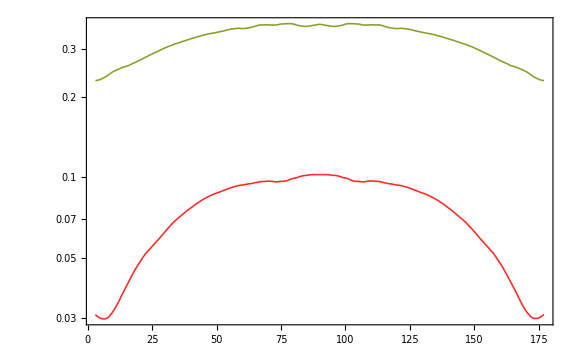

```mathematica
contriInt431PlotPhi=Plot[{CscaInt541Esf135[x],CscaInt541Micro135[x]},{x,3,177},
     
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,greenlight30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\varphi\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito }(\\theta=135^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                             
                                                Style[MaTeX["\\text{Microcito }(\\theta=135^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]
                                                },
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.7}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["contriInt431.svg",contriInt431]
```

contriInt431.svg

```mathematica
CscaInt541EriList130 = Table[
   NIntegrate[(fInterp541Linear[130* Degree, ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}];

CscaInt541EsfList130= Table[
   NIntegrate[(fInterp541LinearEsf[130* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt541MicroList130 = Table[
   NIntegrate[(fInterp541LinearMicro[130* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];
```

```mathematica
CscaInt541Esf130=Interpolation[Transpose[{Range[3,177,1],CscaInt541EsfList130/CscaInt541EriList130}]];
CscaInt541Micro130=Interpolation[Transpose[{Range[3,177,1],CscaInt541MicroList130/CscaInt541EriList130}]];
```

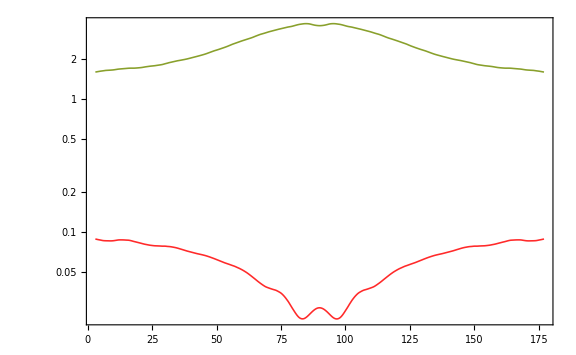

```mathematica
contriInt541PlotPhi130=Plot[{CscaInt541Esf130[x],CscaInt541Micro130[x]},{x,3,177},
     
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,greenlight30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\varphi\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito }(\\theta=130^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                             
                                                Style[MaTeX["\\text{Microcito }(\\theta=130^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]
                                                },
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.7}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["contriInt541PlotPhi130.svg",contriInt541PlotPhi130]
```

contriInt541PlotPhi130.svg

#### Contribuciones integradas en tramos de phi: 573 nm. Pasos de 1

```mathematica
CscaInt573EriList135 = Table[
   NIntegrate[(fInterp573Linear[135* Degree, ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}];

CscaInt573EsfList135= Table[
   NIntegrate[(fInterp573LinearEsf[135* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt573MicroList135 = Table[
   NIntegrate[(fInterp573LinearMicro[135* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];
```

```mathematica
CscaInt573Esf135=Interpolation[Transpose[{Range[3,177,1],CscaInt573EsfList135/CscaInt573EriList135}]]
CscaInt573Micro135=Interpolation[Transpose[{Range[3,177,1],CscaInt573MicroList135/CscaInt573EriList135}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

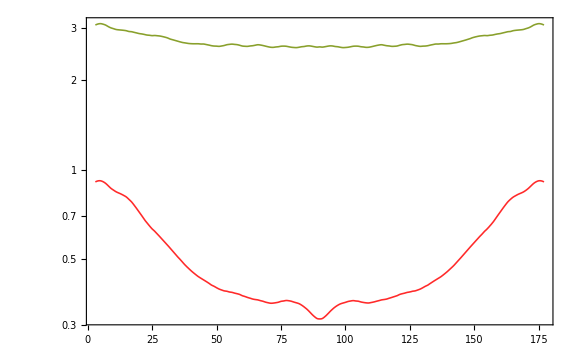

```mathematica
contriInt573PlotPhi=Plot[{CscaInt573Esf135[x],CscaInt573Micro135[x]},{x,3,177},
     
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,greenlight30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\varphi\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito }(\\theta=135^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                             
                                                Style[MaTeX["\\text{Microcito }(\\theta=135^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]
                                                },
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.7}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["contriInt431.svg",contriInt431]
```

contriInt431.svg

```mathematica
CscaInt573EriList130 = Table[
   NIntegrate[(fInterp573Linear[130* Degree, ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}];

CscaInt573EsfList130= Table[
   NIntegrate[(fInterp573LinearEsf[130* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];

CscaInt573MicroList130 = Table[
   NIntegrate[(fInterp573LinearMicro[130* Degree,ph]/(4 Pi)) * Sin[130* Degree], {ph, (i - 3) * Degree, (i + 3) * Degree}],
   {i, 3, 177, 1}
];
```

```mathematica
CscaInt573Esf130=Interpolation[Transpose[{Range[3,177,1],CscaInt573EsfList130/CscaInt573EriList130}]];
CscaInt573Micro130=Interpolation[Transpose[{Range[3,177,1],CscaInt573MicroList130/CscaInt573EriList130}]];
```

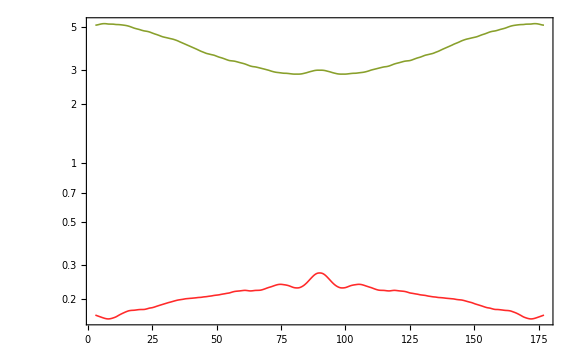

```mathematica
contriInt573PlotPhi130=Plot[{CscaInt573Esf130[x],CscaInt573Micro130[x]},{x,3,177},
     
           PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,greenlight30}),
         
          PlotRange->All,
          ScalingFunctions->"Log",
          FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
          FrameLabel->{{Style[MaTeX["C_{\\text{sca}}^{\\text{enfermo}}/C_{\\text{sca}}^{\\text{sano}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\varphi\\,[\\text{deg}]"],Magnification->1.4],
                                None}},
       
          ImagePadding->{{90,10},{60,20}},
              PlotLegends->Placed[SwatchLegend[{Style[MaTeX["\\text{Esferocito }(\\theta=130^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                             
                                                Style[MaTeX["\\text{Microcito }(\\theta=130^{\\circ})"],FontFamily->"Latin Modern Roman 10",Magnification->1.1]
                                                },
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.2,0.7}],
          ImageSize->Large,
               
            Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["contriInt573PlotPhi130.svg",contriInt573PlotPhi130]
```

contriInt573PlotPhi130.svg